/Users/miawest/Desktop/EtaPrimePhaseTransition

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.22029}. NIntegrate obtained -12.4313+2.06648 ⅈ and 12.4636 for the integral and error estimates.

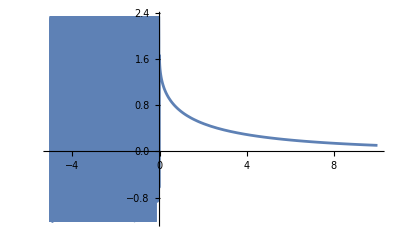

```mathematica
SetDirectory[NotebookDirectory[]]
(*Full integral fails when R^2<0 which can feasably happen*)
Ib[R2_]:=NIntegrate[x^2/(√(x^2+R2))*1/(ⅇ^(√(x^2+R2))-1),{x,0,∞}]

Plot[Re[Ib[R2]],{R2,-5,10}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0000565437}. NIntegrate obtained 1.64477 and 2.89513×10^-13 for the integral and error estimates.

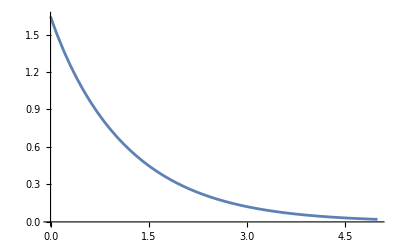

```mathematica
(*Just taking the real component when R^2<0*)
h[R_]:=Re[NIntegrate[ComplexExpand[Re[x^2/(√(x^2+R^2))*1/(ⅇ^(√(x^2+R^2))-1)]/.R->ⅈ R]//Simplify,{x,0,∞},PrecisionGoal->15]]
Plot[h[R],{R,0,5}]
```

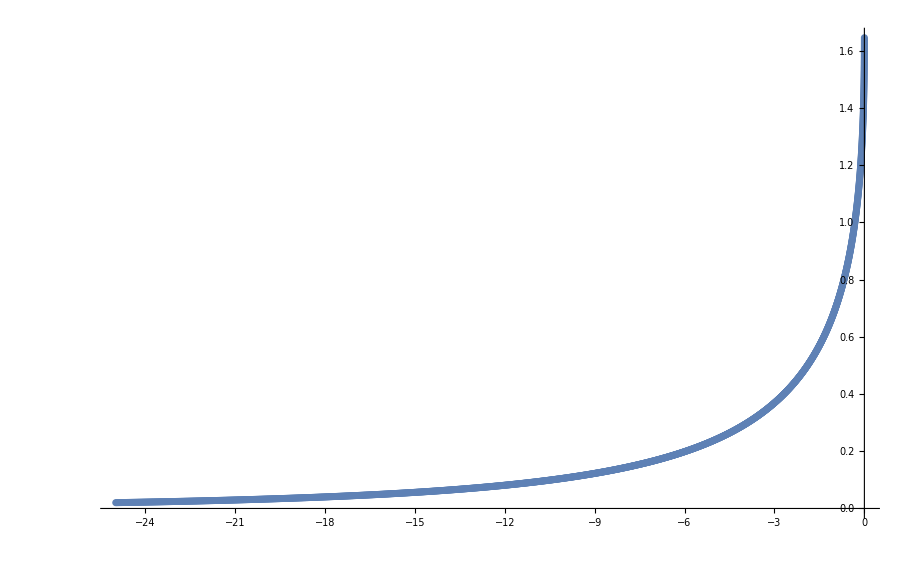

{{-24.98,0.020307},{-24.95,0.0203628},{-24.9201,0.0204188},{-24.8901,0.0204749},{-24.8602,0.0205311},{-24.8303,0.0205875},{-24.8004,0.0206441},{-24.7705,0.0207008},{-24.7407,0.0207577},{-24.7108,0.0208147},{-24.681,0.0208719},{-24.6512,0.0209293},{-24.6214,0.0209868},{-24.5917,0.0210444},{-24.5619,0.0211022},{-24.5322,0.0211602},{-24.5025,0.0212183},{-24.4728,0.0212766},{-24.4431,0.021335},{-24.4135,0.0213936},{-24.3838,0.0214523},{-24.3542,0.0215112},{-24.3246,0.0215703},{-24.295,0.0216295},{-24.2655,0.0216889},{-24.2359,0.0217485},{-24.2064,0.0218082},{-24.1769,0.021868},{-24.1474,0.0219281},{-24.1179,0.0219883},{-24.0885,0.0220486},{-24.059,0.0221091},{-24.0296,0.0221698},{-24.0002,0.0222307},{-23.9708,0.0222917},{-23.9414,0.0223529},{-23.9121,0.0224142},{-23.8828,0.0224757},{-23.8535,0.0225374},{-23.8242,0.0225992},{-23.7949,0.0226612},{-23.7656,0.0227234},{-23.7364,0.0227857},{-23.7072,0.0228482},{-23.678,0.0229109},{-23.6488,0.0229738},{-23.6196,0.0230368},{-23.5904,0.0231},{-23.5613,0.0231633},{-23.5322,0.0232268},{-23.5031,0.0232905},{-23.474,0.0233544},{-23.445,0.0234184},{-23.4159,0.0234827},{-23.3869,0.0235471},{-23.3579,0.0236116},{-23.3289,0.0236764},{-23.2999,0.0237413},{-23.271,0.0238063},{-23.242,0.0238716},{-23.2131,0.023937},{-23.1842,0.0240027},{-23.1553,0.0240685},{-23.1265,0.0241344},{-23.0976,0.0242006},{-23.0688,0.0242669},{-23.04,0.0243334},{-23.0112,0.0244001},{-22.9824,0.0244669},{-22.9537,0.024534},{-22.9249,0.0246012},{-22.8962,0.0246686},{-22.8675,0.0247362},{-22.8388,0.024804},{-22.8102,0.0248719},{-22.7815,0.02494},{-22.7529,0.0250084},{-22.7243,0.0250769},{-22.6957,0.0251455},{-22.6671,0.0252144},{-22.6386,0.0252835},{-22.61,0.0253527},{-22.5815,0.0254221},{-22.553,0.0254918},{-22.5245,0.0255616},{-22.496,0.0256316},{-22.4676,0.0257017},{-22.4392,0.0257721},{-22.4108,0.0258427},{-22.3824,0.0259134},{-22.354,0.0259843},{-22.3256,0.0260555},{-22.2973,0.0261268},{-22.269,0.0261983},{-22.2407,0.02627},{-22.2124,0.0263419},{-22.1841,0.026414},{-22.1558,0.0264863},{-22.1276,0.0265588},{-22.0994,0.0266314},{-22.0712,0.0267043},{-22.043,0.0267774},{-22.0149,0.0268506},{-21.9867,0.0269241},{-21.9586,0.0269978},{-21.9305,0.0270716},{-21.9024,0.0271457},{-21.8743,0.0272199},{-21.8463,0.0272944},{-21.8182,0.027369},{-21.7902,0.0274439},{-21.7622,0.0275189},{-21.7342,0.0275942},{-21.7063,0.0276696},{-21.6783,0.0277453},{-21.6504,0.0278212},{-21.6225,0.0278972},{-21.5946,0.0279735},{-21.5667,0.02805},{-21.5389,0.0281267},{-21.511,0.0282036},{-21.4832,0.0282807},{-21.4554,0.028358},{-21.4276,0.0284355},{-21.3999,0.0285132},{-21.3721,0.0285911},{-21.3444,0.0286693},{-21.3167,0.0287476},{-21.289,0.0288262},{-21.2613,0.0289049},{-21.2337,0.0289839},{-21.206,0.0290631},{-21.1784,0.0291425},{-21.1508,0.0292221},{-21.1232,0.029302},{-21.0956,0.029382},{-21.0681,0.0294623},{-21.0406,0.0295427},{-21.0131,0.0296234},{-20.9856,0.0297043},{-20.9581,0.0297855},{-20.9306,0.0298668},{-20.9032,0.0299484},{-20.8758,0.0300301},{-20.8484,0.0301121},{-20.821,0.0301944},{-20.7936,0.0302768},{-20.7662,0.0303595},{-20.7389,0.0304424},{-20.7116,0.0305255},{-20.6843,0.0306088},{-20.657,0.0306923},{-20.6298,0.0307761},{-20.6025,0.0308601},{-20.5753,0.0309443},{-20.5481,0.0310288},{-20.5209,0.0311135},{-20.4937,0.0311984},{-20.4666,0.0312835},{-20.4394,0.0313689},{-20.4123,0.0314545},{-20.3852,0.0315403},{-20.3581,0.0316263},{-20.3311,0.0317126},{-20.304,0.0317991},{-20.277,0.0318859},{-20.25,0.0319728},{-20.223,0.03206},{-20.196,0.0321475},{-20.1691,0.0322352},{-20.1421,0.0323231},{-20.1152,0.0324112},{-20.0883,0.0324996},{-20.0614,0.0325882},{-20.0346,0.0326771},{-20.0077,0.0327662},{-19.9809,0.0328555},{-19.9541,0.0329451},{-19.9273,0.0330349},{-19.9005,0.0331249},{-19.8738,0.0332152},{-19.847,0.0333058},{-19.8203,0.0333965},{-19.7936,0.0334876},{-19.7669,0.0335788},{-19.7402,0.0336703},{-19.7136,0.0337621},{-19.687,0.0338541},{-19.6604,0.0339463},{-19.6338,0.0340388},{-19.6072,0.0341316},{-19.5806,0.0342245},{-19.5541,0.0343178},{-19.5276,0.0344113},{-19.5011,0.034505},{-19.4746,0.034599},{-19.4481,0.0346932},{-19.4216,0.0347877},{-19.3952,0.0348824},{-19.3688,0.0349774},{-19.3424,0.0350727},{-19.316,0.0351682},{-19.2897,0.035264},{-19.2633,0.03536},{-19.237,0.0354562},{-19.2107,0.0355528},{-19.1844,0.0356496},{-19.1581,0.0357466},{-19.1319,0.0358439},{-19.1056,0.0359415},{-19.0794,0.0360393},{-19.0532,0.0361374},{-19.027,0.0362357},{-19.0009,0.0363343},{-18.9747,0.0364332},{-18.9486,0.0365323},{-18.9225,0.0366318},{-18.8964,0.0367314},{-18.8703,0.0368314},{-18.8443,0.0369316},{-18.8182,0.037032},{-18.7922,0.0371328},{-18.7662,0.0372338},{-18.7402,0.037335},{-18.7143,0.0374366},{-18.6883,0.0375384},{-18.6624,0.0376405},{-18.6365,0.0377429},{-18.6106,0.0378455},{-18.5847,0.0379484},{-18.5589,0.0380516},{-18.533,0.038155},{-18.5072,0.0382588},{-18.4814,0.0383628},{-18.4556,0.0384671},{-18.4298,0.0385716},{-18.4041,0.0386765},{-18.3784,0.0387816},{-18.3527,0.038887},{-18.327,0.0389927},{-18.3013,0.0390987},{-18.2756,0.0392049},{-18.25,0.0393115},{-18.2244,0.0394183},{-18.1988,0.0395254},{-18.1732,0.0396328},{-18.1476,0.0397404},{-18.122,0.0398484},{-18.0965,0.0399567},{-18.071,0.0400652},{-18.0455,0.040174},{-18.02,0.0402831},{-17.9946,0.0403925},{-17.9691,0.0405022},{-17.9437,0.0406122},{-17.9183,0.0407225},{-17.8929,0.0408331},{-17.8675,0.040944},{-17.8422,0.0410551},{-17.8168,0.0411666},{-17.7915,0.0412784},{-17.7662,0.0413904},{-17.7409,0.0415028},{-17.7157,0.0416154},{-17.6904,0.0417284},{-17.6652,0.0418416},{-17.64,0.0419552},{-17.6148,0.0420691},{-17.5896,0.0421832},{-17.5645,0.0422977},{-17.5393,0.0424125},{-17.5142,0.0425275},{-17.4891,0.0426429},{-17.464,0.0427586},{-17.439,0.0428746},{-17.4139,0.0429909},{-17.3889,0.0431075},{-17.3639,0.0432245},{-17.3389,0.0433417},{-17.3139,0.0434593},{-17.289,0.0435771},{-17.264,0.0436953},{-17.2391,0.0438138},{-17.2142,0.0439326},{-17.1893,0.0440517},{-17.1644,0.0441711},{-17.1396,0.0442909},{-17.1148,0.044411},{-17.09,0.0445314},{-17.0652,0.0446521},{-17.0404,0.0447731},{-17.0156,0.0448945},{-16.9909,0.0450161},{-16.9662,0.0451381},{-16.9415,0.0452605},{-16.9168,0.0453831},{-16.8921,0.0455061},{-16.8674,0.0456294},{-16.8428,0.045753},{-16.8182,0.045877},{-16.7936,0.0460013},{-16.769,0.0461259},{-16.7445,0.0462508},{-16.7199,0.0463761},{-16.6954,0.0465017},{-16.6709,0.0466277},{-16.6464,0.0467539},{-16.6219,0.0468806},{-16.5975,0.0470075},{-16.573,0.0471348},{-16.5486,0.0472624},{-16.5242,0.0473904},{-16.4998,0.0475187},{-16.4755,0.0476473},{-16.4511,0.0477763},{-16.4268,0.0479056},{-16.4025,0.0480353},{-16.3782,0.0481653},{-16.3539,0.0482957},{-16.3297,0.0484264},{-16.3054,0.0485574},{-16.2812,0.0486888},{-16.257,0.0488206},{-16.2328,0.0489527},{-16.2087,0.0490851},{-16.1845,0.0492179},{-16.1604,0.0493511},{-16.1363,0.0494846},{-16.1122,0.0496184},{-16.0881,0.0497527},{-16.0641,0.0498872},{-16.04,0.0500222},{-16.016,0.0501574},{-15.992,0.0502931},{-15.968,0.0504291},{-15.944,0.0505654},{-15.9201,0.0507022},{-15.8962,0.0508392},{-15.8723,0.0509767},{-15.8484,0.0511145},{-15.8245,0.0512527},{-15.8006,0.0513912},{-15.7768,0.0515301},{-15.753,0.0516694},{-15.7292,0.0518091},{-15.7054,0.0519491},{-15.6816,0.0520895},{-15.6578,0.0522302},{-15.6341,0.0523713},{-15.6104,0.0525128},{-15.5867,0.0526547},{-15.563,0.052797},{-15.5394,0.0529396},{-15.5157,0.0530826},{-15.4921,0.053226},{-15.4685,0.0533698},{-15.4449,0.0535139},{-15.4213,0.0536584},{-15.3978,0.0538033},{-15.3742,0.0539486},{-15.3507,0.0540943},{-15.3272,0.0542404},{-15.3037,0.0543868},{-15.2803,0.0545337},{-15.2568,0.0546809},{-15.2334,0.0548285},{-15.21,0.0549765},{-15.1866,0.0551249},{-15.1632,0.0552737},{-15.1399,0.0554229},{-15.1165,0.0555724},{-15.0932,0.0557224},{-15.0699,0.0558728},{-15.0466,0.0560235},{-15.0234,0.0561747},{-15.0001,0.0563262},{-14.9769,0.0564782},{-14.9537,0.0566306},{-14.9305,0.0567833},{-14.9073,0.0569365},{-14.8842,0.0570901},{-14.861,0.057244},{-14.8379,0.0573984},{-14.8148,0.0575532},{-14.7917,0.0577084},{-14.7686,0.057864},{-14.7456,0.0580201},{-14.7226,0.0581765},{-14.6996,0.0583333},{-14.6766,0.0584906},{-14.6536,0.0586483},{-14.6306,0.0588064},{-14.6077,0.0589649},{-14.5848,0.0591238},{-14.5619,0.0592831},{-14.539,0.0594429},{-14.5161,0.0596031},{-14.4932,0.0597637},{-14.4704,0.0599247},{-14.4476,0.0600862},{-14.4248,0.0602481},{-14.402,0.0604104},{-14.3793,0.0605731},{-14.3565,0.0607363},{-14.3338,0.0608999},{-14.3111,0.0610639},{-14.2884,0.0612284},{-14.2657,0.0613933},{-14.2431,0.0615586},{-14.2204,0.0617244},{-14.1978,0.0618906},{-14.1752,0.0620572},{-14.1526,0.0622243},{-14.1301,0.0623918},{-14.1075,0.0625598},{-14.085,0.0627282},{-14.0625,0.062897},{-14.04,0.0630663},{-14.0175,0.063236},{-13.9951,0.0634062},{-13.9726,0.0635769},{-13.9502,0.0637479},{-13.9278,0.0639195},{-13.9054,0.0640915},{-13.8831,0.0642639},{-13.8607,0.0644368},{-13.8384,0.0646101},{-13.8161,0.0647839},{-13.7938,0.0649582},{-13.7715,0.0651329},{-13.7493,0.0653081},{-13.727,0.0654837},{-13.7048,0.0656598},{-13.6826,0.0658364},{-13.6604,0.0660134},{-13.6382,0.0661909},{-13.6161,0.0663689},{-13.594,0.0665473},{-13.5719,0.0667262},{-13.5498,0.0669056},{-13.5277,0.0670854},{-13.5056,0.0672657},{-13.4836,0.0674465},{-13.4616,0.0676278},{-13.4396,0.0678095},{-13.4176,0.0679917},{-13.3956,0.0681744},{-13.3736,0.0683576},{-13.3517,0.0685413},{-13.3298,0.0687254},{-13.3079,0.06891},{-13.286,0.0690951},{-13.2642,0.0692807},{-13.2423,0.0694668},{-13.2205,0.0696534},{-13.1987,0.0698404},{-13.1769,0.070028},{-13.1551,0.070216},{-13.1334,0.0704046},{-13.1116,0.0705936},{-13.0899,0.0707831},{-13.0682,0.0709732},{-13.0465,0.0711637},{-13.0249,0.0713547},{-13.0032,0.0715462},{-12.9816,0.0717383},{-12.96,0.0719308},{-12.9384,0.0721238},{-12.9168,0.0723174},{-12.8953,0.0725114},{-12.8737,0.072706},{-12.8522,0.0729011},{-12.8307,0.0730967},{-12.8092,0.0732928},{-12.7878,0.0734894},{-12.7663,0.0736865},{-12.7449,0.0738841},{-12.7235,0.0740823},{-12.7021,0.074281},{-12.6807,0.0744802},{-12.6594,0.0746799},{-12.638,0.0748802},{-12.6167,0.0750809},{-12.5954,0.0752822},{-12.5741,0.0754841},{-12.5528,0.0756864},{-12.5316,0.0758893},{-12.5104,0.0760927},{-12.4892,0.0762967},{-12.468,0.0765012},{-12.4468,0.0767062},{-12.4256,0.0769117},{-12.4045,0.0771178},{-12.3834,0.0773245},{-12.3623,0.0775317},{-12.3412,0.0777394},{-12.3201,0.0779476},{-12.299,0.0781565},{-12.278,0.0783658},{-12.257,0.0785757},{-12.236,0.0787862},{-12.215,0.0789972},{-12.1941,0.0792087},{-12.1731,0.0794208},{-12.1522,0.0796335},{-12.1313,0.0798467},{-12.1104,0.0800605},{-12.0895,0.0802749},{-12.0687,0.0804898},{-12.0478,0.0807052},{-12.027,0.0809212},{-12.0062,0.0811378},{-11.9854,0.081355},{-11.9647,0.0815727},{-11.9439,0.081791},{-11.9232,0.0820099},{-11.9025,0.0822293},{-11.8818,0.0824493},{-11.8611,0.0826699},{-11.8405,0.0828911},{-11.8198,0.0831128},{-11.7992,0.0833351},{-11.7786,0.083558},{-11.758,0.0837815},{-11.7375,0.0840056},{-11.7169,0.0842302},{-11.6964,0.0844555},{-11.6759,0.0846813},{-11.6554,0.0849077},{-11.6349,0.0851347},{-11.6145,0.0853623},{-11.594,0.0855905},{-11.5736,0.0858193},{-11.5532,0.0860487},{-11.5328,0.0862787},{-11.5124,0.0865093},{-11.4921,0.0867405},{-11.4718,0.0869723},{-11.4515,0.0872047},{-11.4312,0.0874377},{-11.4109,0.0876713},{-11.3906,0.0879055},{-11.3704,0.0881404},{-11.3502,0.0883758},{-11.33,0.0886119},{-11.3098,0.0888486},{-11.2896,0.0890859},{-11.2694,0.0893238},{-11.2493,0.0895623},{-11.2292,0.0898015},{-11.2091,0.0900412},{-11.189,0.0902817},{-11.169,0.0905227},{-11.1489,0.0907644},{-11.1289,0.0910066},{-11.1089,0.0912496},{-11.0889,0.0914931},{-11.0689,0.0917373},{-11.049,0.0919821},{-11.029,0.0922276},{-11.0091,0.0924737},{-10.9892,0.0927205},{-10.9693,0.0929678},{-10.9495,0.0932159},{-10.9296,0.0934646},{-10.9098,0.0937139},{-10.89,0.0939639},{-10.8702,0.0942145},{-10.8504,0.0944658},{-10.8307,0.0947177},{-10.8109,0.0949703},{-10.7912,0.0952235},{-10.7715,0.0954775},{-10.7518,0.095732},{-10.7322,0.0959873},{-10.7125,0.0962432},{-10.6929,0.0964997},{-10.6733,0.0967569},{-10.6537,0.0970148},{-10.6341,0.0972734},{-10.6146,0.0975327},{-10.595,0.0977926},{-10.5755,0.0980532},{-10.556,0.0983144},{-10.5365,0.0985764},{-10.517,0.098839},{-10.4976,0.0991023},{-10.4782,0.0993663},{-10.4588,0.099631},{-10.4394,0.0998964},{-10.42,0.100162},{-10.4006,0.100429},{-10.3813,0.100697},{-10.362,0.100965},{-10.3427,0.101234},{-10.3234,0.101503},{-10.3041,0.101773},{-10.2848,0.102044},{-10.2656,0.102316},{-10.2464,0.102588},{-10.2272,0.102861},{-10.208,0.103135},{-10.1889,0.10341},{-10.1697,0.103685},{-10.1506,0.103961},{-10.1315,0.104237},{-10.1124,0.104515},{-10.0933,0.104793},{-10.0743,0.105072},{-10.0552,0.105351},{-10.0362,0.105631},{-10.0172,0.105912},{-9.99824,0.106194},{-9.97928,0.106476},{-9.96034,0.10676},{-9.94141,0.107043},{-9.9225,0.107328},{-9.90361,0.107613},{-9.88474,0.1079},{-9.86588,0.108186},{-9.84704,0.108474},{-9.82823,0.108762},{-9.80942,0.109051},{-9.79064,0.109341},{-9.77188,0.109632},{-9.75313,0.109923},{-9.7344,0.110215},{-9.71569,0.110508},{-9.697,0.110802},{-9.67832,0.111096},{-9.65966,0.111391},{-9.64102,0.111687},{-9.6224,0.111984},{-9.6038,0.112281},{-9.58522,0.112579},{-9.56665,0.112878},{-9.5481,0.113178},{-9.52957,0.113479},{-9.51106,0.11378},{-9.49256,0.114082},{-9.47408,0.114385},{-9.45563,0.114689},{-9.43718,0.114993},{-9.41876,0.115298},{-9.40036,0.115604},{-9.38197,0.115911},{-9.3636,0.116219},{-9.34525,0.116527},{-9.32692,0.116836},{-9.3086,0.117146},{-9.2903,0.117457},{-9.27203,0.117769},{-9.25376,0.118081},{-9.23552,0.118394},{-9.2173,0.118708},{-9.19909,0.119023},{-9.1809,0.119339},{-9.16273,0.119655},{-9.14458,0.119973},{-9.12644,0.120291},{-9.10832,0.12061},{-9.09023,0.120929},{-9.07214,0.12125},{-9.05408,0.121571},{-9.03604,0.121894},{-9.01801,0.122217},{-9.,0.122541},{-8.98201,0.122865},{-8.96404,0.123191},{-8.94608,0.123517},{-8.92814,0.123845},{-8.91022,0.124173},{-8.89232,0.124502},{-8.87444,0.124832},{-8.85658,0.125162},{-8.83873,0.125494},{-8.8209,0.125826},{-8.80309,0.126159},{-8.7853,0.126493},{-8.76752,0.126828},{-8.74976,0.127164},{-8.73203,0.127501},{-8.7143,0.127838},{-8.6966,0.128177},{-8.67892,0.128516},{-8.66125,0.128856},{-8.6436,0.129197},{-8.62597,0.129539},{-8.60836,0.129882},{-8.59076,0.130226},{-8.57318,0.13057},{-8.55563,0.130916},{-8.53808,0.131262},{-8.52056,0.13161},{-8.50306,0.131958},{-8.48557,0.132307},{-8.4681,0.132657},{-8.45065,0.133008},{-8.43322,0.133359},{-8.4158,0.133712},{-8.3984,0.134066},{-8.38103,0.13442},{-8.36366,0.134776},{-8.34632,0.135132},{-8.329,0.135489},{-8.31169,0.135847},{-8.2944,0.136206},{-8.27713,0.136566},{-8.25988,0.136927},{-8.24264,0.137289},{-8.22542,0.137652},{-8.20823,0.138016},{-8.19104,0.13838},{-8.17388,0.138746},{-8.15674,0.139113},{-8.13961,0.13948},{-8.1225,0.139848},{-8.10541,0.140218},{-8.08834,0.140588},{-8.07128,0.140959},{-8.05424,0.141332},{-8.03723,0.141705},{-8.02022,0.142079},{-8.00324,0.142454},{-7.98628,0.14283},{-7.96933,0.143207},{-7.9524,0.143585},{-7.93549,0.143964},{-7.9186,0.144344},{-7.90172,0.144725},{-7.88486,0.145107},{-7.86803,0.14549},{-7.8512,0.145874},{-7.8344,0.146259},{-7.81762,0.146645},{-7.80085,0.147032},{-7.7841,0.14742},{-7.76737,0.147808},{-7.75066,0.148198},{-7.73396,0.148589},{-7.71728,0.148981},{-7.70063,0.149374},{-7.68398,0.149768},{-7.66736,0.150163},{-7.65076,0.150559},{-7.63417,0.150956},{-7.6176,0.151353},{-7.60105,0.151752},{-7.58452,0.152152},{-7.568,0.152553},{-7.5515,0.152956},{-7.53503,0.153359},{-7.51856,0.153763},{-7.50212,0.154168},{-7.4857,0.154574},{-7.46929,0.154981},{-7.4529,0.15539},{-7.43653,0.155799},{-7.42018,0.156209},{-7.40384,0.156621},{-7.38752,0.157033},{-7.37122,0.157447},{-7.35494,0.157861},{-7.33868,0.158277},{-7.32244,0.158694},{-7.30621,0.159112},{-7.29,0.159531},{-7.27381,0.15995},{-7.25764,0.160371},{-7.24148,0.160794},{-7.22534,0.161217},{-7.20923,0.161641},{-7.19312,0.162066},{-7.17704,0.162493},{-7.16098,0.16292},{-7.14493,0.163349},{-7.1289,0.163779},{-7.11289,0.16421},{-7.0969,0.164642},{-7.08092,0.165075},{-7.06496,0.165509},{-7.04903,0.165944},{-7.0331,0.166381},{-7.0172,0.166818},{-7.00132,0.167257},{-6.98545,0.167696},{-6.9696,0.168137},{-6.95377,0.168579},{-6.93796,0.169022},{-6.92216,0.169467},{-6.90638,0.169912},{-6.89063,0.170359},{-6.87488,0.170806},{-6.85916,0.171255},{-6.84346,0.171705},{-6.82777,0.172156},{-6.8121,0.172609},{-6.79645,0.173062},{-6.78082,0.173517},{-6.7652,0.173973},{-6.7496,0.174429},{-6.73403,0.174888},{-6.71846,0.175347},{-6.70292,0.175807},{-6.6874,0.176269},{-6.67189,0.176732},{-6.6564,0.177196},{-6.64093,0.177661},{-6.62548,0.178127},{-6.61004,0.178595},{-6.59462,0.179064},{-6.57923,0.179534},{-6.56384,0.180005},{-6.54848,0.180477},{-6.53314,0.180951},{-6.51781,0.181426},{-6.5025,0.181902},{-6.48721,0.182379},{-6.47194,0.182857},{-6.45668,0.183337},{-6.44144,0.183818},{-6.42623,0.1843},{-6.41102,0.184783},{-6.39584,0.185268},{-6.38068,0.185754},{-6.36553,0.186241},{-6.3504,0.186729},{-6.33529,0.187218},{-6.3202,0.187709},{-6.30512,0.188201},{-6.29006,0.188695},{-6.27502,0.189189},{-6.26,0.189685},{-6.245,0.190182},{-6.23002,0.19068},{-6.21505,0.19118},{-6.2001,0.191681},{-6.18517,0.192183},{-6.17026,0.192687},{-6.15536,0.193191},{-6.14048,0.193697},{-6.12563,0.194205},{-6.11078,0.194713},{-6.09596,0.195223},{-6.08116,0.195735},{-6.06637,0.196247},{-6.0516,0.196761},{-6.03685,0.197276},{-6.02212,0.197792},{-6.0074,0.19831},{-5.9927,0.198829},{-5.97802,0.19935},{-5.96336,0.199872},{-5.94872,0.200395},{-5.9341,0.200919},{-5.91949,0.201445},{-5.9049,0.201972},{-5.89033,0.2025},{-5.87578,0.20303},{-5.86124,0.203561},{-5.84672,0.204094},{-5.83223,0.204627},{-5.81774,0.205163},{-5.80328,0.205699},{-5.78884,0.206237},{-5.77441,0.206776},{-5.76,0.207317},{-5.74561,0.207859},{-5.73124,0.208402},{-5.71688,0.208947},{-5.70254,0.209493},{-5.68823,0.210041},{-5.67392,0.21059},{-5.65964,0.21114},{-5.64538,0.211692},{-5.63113,0.212245},{-5.6169,0.2128},{-5.60269,0.213356},{-5.5885,0.213913},{-5.57432,0.214472},{-5.56016,0.215032},{-5.54603,0.215594},{-5.5319,0.216157},{-5.5178,0.216722},{-5.50372,0.217288},{-5.48965,0.217855},{-5.4756,0.218424},{-5.46157,0.218994},{-5.44756,0.219566},{-5.43356,0.220139},{-5.41958,0.220714},{-5.40563,0.22129},{-5.39168,0.221867},{-5.37776,0.222447},{-5.36386,0.223027},{-5.34997,0.223609},{-5.3361,0.224193},{-5.32225,0.224777},{-5.30842,0.225364},{-5.2946,0.225952},{-5.2808,0.226541},{-5.26702,0.227132},{-5.25326,0.227725},{-5.23952,0.228319},{-5.2258,0.228914},{-5.21209,0.229511},{-5.1984,0.230109},{-5.18473,0.230709},{-5.17108,0.231311},{-5.15744,0.231914},{-5.14382,0.232519},{-5.13023,0.233125},{-5.11664,0.233732},{-5.10308,0.234341},{-5.08954,0.234952},{-5.07601,0.235565},{-5.0625,0.236178},{-5.04901,0.236794},{-5.03554,0.237411},{-5.02208,0.238029},{-5.00864,0.238649},{-4.99523,0.239271},{-4.98182,0.239894},{-4.96844,0.240519},{-4.95508,0.241145},{-4.94173,0.241773},{-4.9284,0.242403},{-4.91509,0.243034},{-4.9018,0.243667},{-4.88852,0.244301},{-4.87526,0.244937},{-4.86203,0.245575},{-4.8488,0.246214},{-4.8356,0.246855},{-4.82242,0.247498},{-4.80925,0.248142},{-4.7961,0.248787},{-4.78297,0.249435},{-4.76986,0.250084},{-4.75676,0.250735},{-4.74368,0.251387},{-4.73063,0.252041},{-4.71758,0.252696},{-4.70456,0.253354},{-4.69156,0.254013},{-4.67857,0.254673},{-4.6656,0.255336},{-4.65265,0.256},{-4.63972,0.256665},{-4.6268,0.257333},{-4.6139,0.258002},{-4.60103,0.258672},{-4.58816,0.259345},{-4.57532,0.260019},{-4.5625,0.260695},{-4.54969,0.261372},{-4.5369,0.262051},{-4.52413,0.262732},{-4.51138,0.263415},{-4.49864,0.2641},{-4.48592,0.264786},{-4.47323,0.265474},{-4.46054,0.266163},{-4.44788,0.266855},{-4.43524,0.267548},{-4.42261,0.268243},{-4.41,0.268939},{-4.39741,0.269638},{-4.38484,0.270338},{-4.37228,0.27104},{-4.35974,0.271744},{-4.34723,0.272449},{-4.33472,0.273156},{-4.32224,0.273865},{-4.30978,0.274576},{-4.29733,0.275289},{-4.2849,0.276003},{-4.27249,0.27672},{-4.2601,0.277438},{-4.24772,0.278158},{-4.23536,0.27888},{-4.22303,0.279603},{-4.2107,0.280328},{-4.1984,0.281056},{-4.18612,0.281785},{-4.17385,0.282516},{-4.1616,0.283248},{-4.14937,0.283983},{-4.13716,0.284719},{-4.12496,0.285458},{-4.11278,0.286198},{-4.10063,0.28694},{-4.08848,0.287684},{-4.07636,0.28843},{-4.06426,0.289177},{-4.05217,0.289927},{-4.0401,0.290679},{-4.02805,0.291432},{-4.01602,0.292187},{-4.004,0.292944},{-3.992,0.293703},{-3.98003,0.294465},{-3.96806,0.295227},{-3.95612,0.295992},{-3.9442,0.296759},{-3.93229,0.297528},{-3.9204,0.298299},{-3.90853,0.299071},{-3.89668,0.299846},{-3.88484,0.300622},{-3.87302,0.301401},{-3.86123,0.302181},{-3.84944,0.302964},{-3.83768,0.303748},{-3.82594,0.304535},{-3.81421,0.305323},{-3.8025,0.306113},{-3.79081,0.306906},{-3.77914,0.3077},{-3.76748,0.308496},{-3.75584,0.309295},{-3.74423,0.310095},{-3.73262,0.310898},{-3.72104,0.311702},{-3.70948,0.312508},{-3.69793,0.313317},{-3.6864,0.314127},{-3.67489,0.31494},{-3.6634,0.315755},{-3.65192,0.316571},{-3.64046,0.31739},{-3.62903,0.318211},{-3.6176,0.319034},{-3.6062,0.319859},{-3.59482,0.320686},{-3.58345,0.321515},{-3.5721,0.322346},{-3.56077,0.32318},{-3.54946,0.324015},{-3.53816,0.324853},{-3.52688,0.325692},{-3.51563,0.326534},{-3.50438,0.327378},{-3.49316,0.328224},{-3.48196,0.329072},{-3.47077,0.329922},{-3.4596,0.330775},{-3.44845,0.331629},{-3.43732,0.332486},{-3.4262,0.333345},{-3.4151,0.334206},{-3.40403,0.335069},{-3.39296,0.335935},{-3.38192,0.336802},{-3.3709,0.337672},{-3.35989,0.338544},{-3.3489,0.339418},{-3.33793,0.340294},{-3.32698,0.341173},{-3.31604,0.342054},{-3.30512,0.342937},{-3.29423,0.343822},{-3.28334,0.34471},{-3.27248,0.345599},{-3.26164,0.346491},{-3.25081,0.347385},{-3.24,0.348282},{-3.22921,0.349181},{-3.21844,0.350082},{-3.20768,0.350985},{-3.19694,0.35189},{-3.18623,0.352798},{-3.17552,0.353708},{-3.16484,0.354621},{-3.15418,0.355535},{-3.14353,0.356452},{-3.1329,0.357372},{-3.12229,0.358293},{-3.1117,0.359217},{-3.10112,0.360143},{-3.09056,0.361072},{-3.08003,0.362003},{-3.0695,0.362936},{-3.059,0.363872},{-3.04852,0.36481},{-3.03805,0.36575},{-3.0276,0.366693},{-3.01717,0.367638},{-3.00676,0.368585},{-2.99636,0.369535},{-2.98598,0.370488},{-2.97563,0.371442},{-2.96528,0.372399},{-2.95496,0.373359},{-2.94466,0.374321},{-2.93437,0.375285},{-2.9241,0.376252},{-2.91385,0.377221},{-2.90362,0.378192},{-2.8934,0.379167},{-2.8832,0.380143},{-2.87303,0.381122},{-2.86286,0.382103},{-2.85272,0.383087},{-2.8426,0.384074},{-2.83249,0.385063},{-2.8224,0.386054},{-2.81233,0.387048},{-2.80228,0.388044},{-2.79224,0.389043},{-2.78222,0.390044},{-2.77223,0.391048},{-2.76224,0.392055},{-2.75228,0.393064},{-2.74234,0.394075},{-2.73241,0.395089},{-2.7225,0.396106},{-2.71261,0.397125},{-2.70274,0.398147},{-2.69288,0.399171},{-2.68304,0.400198},{-2.67323,0.401227},{-2.66342,0.40226},{-2.65364,0.403294},{-2.64388,0.404331},{-2.63413,0.405371},{-2.6244,0.406414},{-2.61469,0.407459},{-2.605,0.408507},{-2.59532,0.409557},{-2.58566,0.41061},{-2.57603,0.411666},{-2.5664,0.412724},{-2.5568,0.413785},{-2.54722,0.414849},{-2.53765,0.415915},{-2.5281,0.416984},{-2.51857,0.418056},{-2.50906,0.41913},{-2.49956,0.420207},{-2.49008,0.421287},{-2.48063,0.42237},{-2.47118,0.423455},{-2.46176,0.424543},{-2.45236,0.425634},{-2.44297,0.426727},{-2.4336,0.427824},{-2.42425,0.428923},{-2.41492,0.430025},{-2.4056,0.431129},{-2.3963,0.432236},{-2.38703,0.433347},{-2.37776,0.434459},{-2.36852,0.435575},{-2.3593,0.436694},{-2.35009,0.437815},{-2.3409,0.438939},{-2.33173,0.440066},{-2.32258,0.441196},{-2.31344,0.442329},{-2.30432,0.443464},{-2.29523,0.444603},{-2.28614,0.445744},{-2.27708,0.446888},{-2.26804,0.448035},{-2.25901,0.449185},{-2.25,0.450338},{-2.24101,0.451494},{-2.23204,0.452652},{-2.22308,0.453814},{-2.21414,0.454978},{-2.20523,0.456146},{-2.19632,0.457316},{-2.18744,0.458489},{-2.17858,0.459666},{-2.16973,0.460845},{-2.1609,0.462027},{-2.15209,0.463212},{-2.1433,0.4644},{-2.13452,0.465591},{-2.12576,0.466785},{-2.11703,0.467983},{-2.1083,0.469183},{-2.0996,0.470386},{-2.09092,0.471592},{-2.08225,0.472801},{-2.0736,0.474014},{-2.06497,0.475229},{-2.05636,0.476448},{-2.04776,0.477669},{-2.03918,0.478894},{-2.03063,0.480121},{-2.02208,0.481352},{-2.01356,0.482586},{-2.00506,0.483823},{-1.99657,0.485063},{-1.9881,0.486306},{-1.97965,0.487552},{-1.97122,0.488802},{-1.9628,0.490054},{-1.9544,0.49131},{-1.94603,0.492569},{-1.93766,0.493831},{-1.92932,0.495097},{-1.921,0.496365},{-1.91269,0.497637},{-1.9044,0.498912},{-1.89613,0.50019},{-1.88788,0.501471},{-1.87964,0.502756},{-1.87142,0.504044},{-1.86323,0.505335},{-1.85504,0.506629},{-1.84688,0.507926},{-1.83874,0.509227},{-1.83061,0.510531},{-1.8225,0.511839},{-1.81441,0.51315},{-1.80634,0.514464},{-1.79828,0.515781},{-1.79024,0.517102},{-1.78223,0.518426},{-1.77422,0.519753},{-1.76624,0.521084},{-1.75828,0.522418},{-1.75033,0.523755},{-1.7424,0.525096},{-1.73449,0.52644},{-1.7266,0.527788},{-1.71872,0.529139},{-1.71086,0.530493},{-1.70302,0.531851},{-1.6952,0.533212},{-1.6874,0.534577},{-1.67962,0.535945},{-1.67185,0.537316},{-1.6641,0.538691},{-1.65637,0.54007},{-1.64866,0.541452},{-1.64096,0.542837},{-1.63328,0.544226},{-1.62563,0.545619},{-1.61798,0.547015},{-1.61036,0.548415},{-1.60276,0.549818},{-1.59517,0.551224},{-1.5876,0.552634},{-1.58005,0.554048},{-1.57252,0.555465},{-1.565,0.556886},{-1.5575,0.558311},{-1.55003,0.559739},{-1.54256,0.561171},{-1.53512,0.562606},{-1.5277,0.564045},{-1.52029,0.565488},{-1.5129,0.566934},{-1.50553,0.568384},{-1.49818,0.569837},{-1.49084,0.571295},{-1.48352,0.572756},{-1.47623,0.57422},{-1.46894,0.575689},{-1.46168,0.577161},{-1.45444,0.578636},{-1.44721,0.580116},{-1.44,0.581599},{-1.43281,0.583086},{-1.42564,0.584577},{-1.41848,0.586072},{-1.41134,0.58757},{-1.40423,0.589072},{-1.39712,0.590578},{-1.39004,0.592088},{-1.38298,0.593601},{-1.37593,0.595119},{-1.3689,0.59664},{-1.36189,0.598165},{-1.3549,0.599694},{-1.34792,0.601227},{-1.34096,0.602764},{-1.33403,0.604305},{-1.3271,0.605849},{-1.3202,0.607398},{-1.31332,0.60895},{-1.30645,0.610507},{-1.2996,0.612067},{-1.29277,0.613631},{-1.28596,0.6152},{-1.27916,0.616772},{-1.27238,0.618348},{-1.26563,0.619928},{-1.25888,0.621512},{-1.25216,0.623101},{-1.24546,0.624693},{-1.23877,0.626289},{-1.2321,0.62789},{-1.22545,0.629494},{-1.21882,0.631103},{-1.2122,0.632715},{-1.2056,0.634332},{-1.19903,0.635953},{-1.19246,0.637578},{-1.18592,0.639207},{-1.1794,0.64084},{-1.17289,0.642478},{-1.1664,0.644119},{-1.15993,0.645765},{-1.15348,0.647415},{-1.14704,0.649069},{-1.14062,0.650728},{-1.13422,0.65239},{-1.12784,0.654057},{-1.12148,0.655728},{-1.11514,0.657403},{-1.10881,0.659083},{-1.1025,0.660767},{-1.09621,0.662455},{-1.08994,0.664148},{-1.08368,0.665844},{-1.07744,0.667545},{-1.07122,0.669251},{-1.06502,0.670961},{-1.05884,0.672675},{-1.05268,0.674393},{-1.04653,0.676116},{-1.0404,0.677844},{-1.03429,0.679575},{-1.0282,0.681312},{-1.02212,0.683052},{-1.01606,0.684797},{-1.01003,0.686547},{-1.004,0.688301},{-0.998001,0.690059},{-0.992016,0.691822},{-0.986049,0.69359},{-0.9801,0.695361},{-0.974169,0.697138},{-0.968256,0.698919},{-0.962361,0.700705},{-0.956484,0.702495},{-0.950625,0.70429},{-0.944784,0.706089},{-0.938961,0.707893},{-0.933156,0.709702},{-0.927369,0.711515},{-0.9216,0.713333},{-0.915849,0.715155},{-0.910116,0.716983},{-0.904401,0.718814},{-0.898704,0.720651},{-0.893025,0.722492},{-0.887364,0.724338},{-0.881721,0.726189},{-0.876096,0.728045},{-0.870489,0.729905},{-0.8649,0.73177},{-0.859329,0.73364},{-0.853776,0.735515},{-0.848241,0.737394},{-0.842724,0.739279},{-0.837225,0.741168},{-0.831744,0.743062},{-0.826281,0.744961},{-0.820836,0.746864},{-0.815409,0.748773},{-0.81,0.750687},{-0.804609,0.752605},{-0.799236,0.754529},{-0.793881,0.756457},{-0.788544,0.758391},{-0.783225,0.760329},{-0.777924,0.762272},{-0.772641,0.764221},{-0.767376,0.766174},{-0.762129,0.768133},{-0.7569,0.770096},{-0.751689,0.772065},{-0.746496,0.774039},{-0.741321,0.776018},{-0.736164,0.778001},{-0.731025,0.77999},{-0.725904,0.781985},{-0.720801,0.783984},{-0.715716,0.785989},{-0.710649,0.787998},{-0.7056,0.790013},{-0.700569,0.792033},{-0.695556,0.794059},{-0.690561,0.796089},{-0.685584,0.798125},{-0.680625,0.800166},{-0.675684,0.802213},{-0.670761,0.804265},{-0.665856,0.806322},{-0.660969,0.808384},{-0.6561,0.810452},{-0.651249,0.812525},{-0.646416,0.814604},{-0.641601,0.816688},{-0.636804,0.818777},{-0.632025,0.820872},{-0.627264,0.822972},{-0.622521,0.825078},{-0.617796,0.827189},{-0.613089,0.829306},{-0.6084,0.831428},{-0.603729,0.833556},{-0.599076,0.835689},{-0.594441,0.837828},{-0.589824,0.839972},{-0.585225,0.842122},{-0.580644,0.844278},{-0.576081,0.846439},{-0.571536,0.848606},{-0.567009,0.850779},{-0.5625,0.852957},{-0.558009,0.855141},{-0.553536,0.857331},{-0.549081,0.859527},{-0.544644,0.861728},{-0.540225,0.863935},{-0.535824,0.866148},{-0.531441,0.868366},{-0.527076,0.870591},{-0.522729,0.872821},{-0.5184,0.875057},{-0.514089,0.877299},{-0.509796,0.879547},{-0.505521,0.881801},{-0.501264,0.88406},{-0.497025,0.886326},{-0.492804,0.888598},{-0.488601,0.890875},{-0.484416,0.893159},{-0.480249,0.895448},{-0.4761,0.897744},{-0.471969,0.900046},{-0.467856,0.902354},{-0.463761,0.904668},{-0.459684,0.906988},{-0.455625,0.909314},{-0.451584,0.911646},{-0.447561,0.913985},{-0.443556,0.916329},{-0.439569,0.91868},{-0.4356,0.921037},{-0.431649,0.923401},{-0.427716,0.92577},{-0.423801,0.928146},{-0.419904,0.930528},{-0.416025,0.932917},{-0.412164,0.935312},{-0.408321,0.937713},{-0.404496,0.940121},{-0.400689,0.942535},{-0.3969,0.944955},{-0.393129,0.947382},{-0.389376,0.949816},{-0.385641,0.952256},{-0.381924,0.954702},{-0.378225,0.957155},{-0.374544,0.959615},{-0.370881,0.962081},{-0.367236,0.964554},{-0.363609,0.967033},{-0.36,0.969519},{-0.356409,0.972012},{-0.352836,0.974511},{-0.349281,0.977017},{-0.345744,0.97953},{-0.342225,0.982049},{-0.338724,0.984576},{-0.335241,0.987109},{-0.331776,0.989649},{-0.328329,0.992195},{-0.3249,0.994749},{-0.321489,0.99731},{-0.318096,0.999877},{-0.314721,1.00245},{-0.311364,1.00503},{-0.308025,1.00762},{-0.304704,1.01022},{-0.301401,1.01282},{-0.298116,1.01543},{-0.294849,1.01804},{-0.2916,1.02067},{-0.288369,1.0233},{-0.285156,1.02594},{-0.281961,1.02858},{-0.278784,1.03123},{-0.275625,1.03389},{-0.272484,1.03656},{-0.269361,1.03923},{-0.266256,1.04191},{-0.263169,1.0446},{-0.2601,1.0473},{-0.257049,1.05},{-0.254016,1.05271},{-0.251001,1.05543},{-0.248004,1.05816},{-0.245025,1.06089},{-0.242064,1.06363},{-0.239121,1.06638},{-0.236196,1.06913},{-0.233289,1.0719},{-0.2304,1.07467},{-0.227529,1.07745},{-0.224676,1.08023},{-0.221841,1.08303},{-0.219024,1.08583},{-0.216225,1.08864},{-0.213444,1.09146},{-0.210681,1.09428},{-0.207936,1.09711},{-0.205209,1.09995},{-0.2025,1.1028},{-0.199809,1.10566},{-0.197136,1.10852},{-0.194481,1.1114},{-0.191844,1.11428},{-0.189225,1.11716},{-0.186624,1.12006},{-0.184041,1.12297},{-0.181476,1.12588},{-0.178929,1.1288},{-0.1764,1.13173},{-0.173889,1.13467},{-0.171396,1.13761},{-0.168921,1.14057},{-0.166464,1.14353},{-0.164025,1.1465},{-0.161604,1.14948},{-0.159201,1.15246},{-0.156816,1.15546},{-0.154449,1.15847},{-0.1521,1.16148},{-0.149769,1.1645},{-0.147456,1.16753},{-0.145161,1.17057},{-0.142884,1.17362},{-0.140625,1.17667},{-0.138384,1.17974},{-0.136161,1.18281},{-0.133956,1.18589},{-0.131769,1.18898},{-0.1296,1.19208},{-0.127449,1.19519},{-0.125316,1.19831},{-0.123201,1.20144},{-0.121104,1.20457},{-0.119025,1.20772},{-0.116964,1.21087},{-0.114921,1.21404},{-0.112896,1.21721},{-0.110889,1.22039},{-0.1089,1.22358},{-0.106929,1.22678},{-0.104976,1.22999},{-0.103041,1.23321},{-0.101124,1.23644},{-0.099225,1.23968},{-0.097344,1.24292},{-0.095481,1.24618},{-0.093636,1.24945},{-0.091809,1.25272},{-0.09,1.25601},{-0.088209,1.25931},{-0.086436,1.26261},{-0.084681,1.26593},{-0.082944,1.26925},{-0.081225,1.27259},{-0.079524,1.27593},{-0.077841,1.27929},{-0.076176,1.28265},{-0.074529,1.28603},{-0.0729,1.28941},{-0.071289,1.29281},{-0.069696,1.29621},{-0.068121,1.29963},{-0.066564,1.30306},{-0.065025,1.30649},{-0.063504,1.30994},{-0.062001,1.3134},{-0.060516,1.31687},{-0.059049,1.32034},{-0.0576,1.32383},{-0.056169,1.32733},{-0.054756,1.33085},{-0.053361,1.33437},{-0.051984,1.3379},{-0.050625,1.34144},{-0.049284,1.345},{-0.047961,1.34857},{-0.046656,1.35214},{-0.045369,1.35573},{-0.0441,1.35933},{-0.042849,1.36294},{-0.041616,1.36656},{-0.040401,1.3702},{-0.039204,1.37384},{-0.038025,1.3775},{-0.036864,1.38117},{-0.035721,1.38485},{-0.034596,1.38854},{-0.033489,1.39224},{-0.0324,1.39596},{-0.031329,1.39969},{-0.030276,1.40343},{-0.029241,1.40718},{-0.028224,1.41094},{-0.027225,1.41472},{-0.026244,1.41851},{-0.025281,1.42231},{-0.024336,1.42612},{-0.023409,1.42995},{-0.0225,1.43379},{-0.021609,1.43764},{-0.020736,1.44151},{-0.019881,1.44539},{-0.019044,1.44928},{-0.018225,1.45318},{-0.017424,1.4571},{-0.016641,1.46103},{-0.015876,1.46498},{-0.015129,1.46893},{-0.0144,1.47291},{-0.013689,1.47689},{-0.012996,1.48089},{-0.012321,1.48491},{-0.011664,1.48893},{-0.011025,1.49298},{-0.010404,1.49703},{-0.009801,1.5011},{-0.009216,1.50519},{-0.008649,1.50929},{-0.0081,1.51341},{-0.007569,1.51754},{-0.007056,1.52169},{-0.006561,1.52585},{-0.006084,1.53002},{-0.005625,1.53422},{-0.005184,1.53843},{-0.004761,1.54265},{-0.004356,1.54689},{-0.003969,1.55115},{-0.0036,1.55543},{-0.003249,1.55972},{-0.002916,1.56403},{-0.002601,1.56835},{-0.002304,1.5727},{-0.002025,1.57706},{-0.001764,1.58144},{-0.001521,1.58584},{-0.001296,1.59026},{-0.001089,1.59469},{-0.0009,1.59915},{-0.000729,1.60363},{-0.000576,1.60813},{-0.000441,1.61264},{-0.000324,1.61718},{-0.000225,1.62175},{-0.000144,1.62633},{-0.000081,1.63094},{-0.000036,1.63558},{-9.×10^-6,1.64024},{0.,1.64493}}

```mathematica
IbNegs=Table[h[R],{R,0,5,0.003}];
R2Negs=Table[-R^2,{R,0,5,0.003}];

ListPlot[Table[{R2Negs[[a]],IbNegs[[a]]},{a,Length[R2Negs]}]]

data=Reverse[Transpose[{R2Negs,IbNegs}]]
```

```mathematica
Export["IbDataR2Negative.csv",data]
```

IbDataR2Negative.csv

```mathematica
data
```

{{-24.98,0.020307},{-24.95,0.0203628},{-24.9201,0.0204188},{-24.8901,0.0204749},{-24.8602,0.0205311},{-24.8303,0.0205875},{-24.8004,0.0206441},{-24.7705,0.0207008},{-24.7407,0.0207577},{-24.7108,0.0208147},{-24.681,0.0208719},{-24.6512,0.0209293},{-24.6214,0.0209868},{-24.5917,0.0210444},{-24.5619,0.0211022},{-24.5322,0.0211602},{-24.5025,0.0212183},{-24.4728,0.0212766},{-24.4431,0.021335},{-24.4135,0.0213936},{-24.3838,0.0214523},{-24.3542,0.0215112},{-24.3246,0.0215703},{-24.295,0.0216295},{-24.2655,0.0216889},{-24.2359,0.0217485},{-24.2064,0.0218082},{-24.1769,0.021868},{-24.1474,0.0219281},{-24.1179,0.0219883},{-24.0885,0.0220486},{-24.059,0.0221091},{-24.0296,0.0221698},{-24.0002,0.0222307},{-23.9708,0.0222917},{-23.9414,0.0223529},{-23.9121,0.0224142},{-23.8828,0.0224757},{-23.8535,0.0225374},{-23.8242,0.0225992},{-23.7949,0.0226612},{-23.7656,0.0227234},{-23.7364,0.0227857},{-23.7072,0.0228482},{-23.678,0.0229109},{-23.6488,0.0229738},{-23.6196,0.0230368},{-23.5904,0.0231},{-23.5613,0.0231633},{-23.5322,0.0232268},{-23.5031,0.0232905},{-23.474,0.0233544},{-23.445,0.0234184},{-23.4159,0.0234827},{-23.3869,0.0235471},{-23.3579,0.0236116},{-23.3289,0.0236764},{-23.2999,0.0237413},{-23.271,0.0238063},{-23.242,0.0238716},{-23.2131,0.023937},{-23.1842,0.0240027},{-23.1553,0.0240685},{-23.1265,0.0241344},{-23.0976,0.0242006},{-23.0688,0.0242669},{-23.04,0.0243334},{-23.0112,0.0244001},{-22.9824,0.0244669},{-22.9537,0.024534},{-22.9249,0.0246012},{-22.8962,0.0246686},{-22.8675,0.0247362},{-22.8388,0.024804},{-22.8102,0.0248719},{-22.7815,0.02494},{-22.7529,0.0250084},{-22.7243,0.0250769},{-22.6957,0.0251455},{-22.6671,0.0252144},{-22.6386,0.0252835},{-22.61,0.0253527},{-22.5815,0.0254221},{-22.553,0.0254918},{-22.5245,0.0255616},{-22.496,0.0256316},{-22.4676,0.0257017},{-22.4392,0.0257721},{-22.4108,0.0258427},{-22.3824,0.0259134},{-22.354,0.0259843},{-22.3256,0.0260555},{-22.2973,0.0261268},{-22.269,0.0261983},{-22.2407,0.02627},{-22.2124,0.0263419},{-22.1841,0.026414},{-22.1558,0.0264863},{-22.1276,0.0265588},{-22.0994,0.0266314},{-22.0712,0.0267043},{-22.043,0.0267774},{-22.0149,0.0268506},{-21.9867,0.0269241},{-21.9586,0.0269978},{-21.9305,0.0270716},{-21.9024,0.0271457},{-21.8743,0.0272199},{-21.8463,0.0272944},{-21.8182,0.027369},{-21.7902,0.0274439},{-21.7622,0.0275189},{-21.7342,0.0275942},{-21.7063,0.0276696},{-21.6783,0.0277453},{-21.6504,0.0278212},{-21.6225,0.0278972},{-21.5946,0.0279735},{-21.5667,0.02805},{-21.5389,0.0281267},{-21.511,0.0282036},{-21.4832,0.0282807},{-21.4554,0.028358},{-21.4276,0.0284355},{-21.3999,0.0285132},{-21.3721,0.0285911},{-21.3444,0.0286693},{-21.3167,0.0287476},{-21.289,0.0288262},{-21.2613,0.0289049},{-21.2337,0.0289839},{-21.206,0.0290631},{-21.1784,0.0291425},{-21.1508,0.0292221},{-21.1232,0.029302},{-21.0956,0.029382},{-21.0681,0.0294623},{-21.0406,0.0295427},{-21.0131,0.0296234},{-20.9856,0.0297043},{-20.9581,0.0297855},{-20.9306,0.0298668},{-20.9032,0.0299484},{-20.8758,0.0300301},{-20.8484,0.0301121},{-20.821,0.0301944},{-20.7936,0.0302768},{-20.7662,0.0303595},{-20.7389,0.0304424},{-20.7116,0.0305255},{-20.6843,0.0306088},{-20.657,0.0306923},{-20.6298,0.0307761},{-20.6025,0.0308601},{-20.5753,0.0309443},{-20.5481,0.0310288},{-20.5209,0.0311135},{-20.4937,0.0311984},{-20.4666,0.0312835},{-20.4394,0.0313689},{-20.4123,0.0314545},{-20.3852,0.0315403},{-20.3581,0.0316263},{-20.3311,0.0317126},{-20.304,0.0317991},{-20.277,0.0318859},{-20.25,0.0319728},{-20.223,0.03206},{-20.196,0.0321475},{-20.1691,0.0322352},{-20.1421,0.0323231},{-20.1152,0.0324112},{-20.0883,0.0324996},{-20.0614,0.0325882},{-20.0346,0.0326771},{-20.0077,0.0327662},{-19.9809,0.0328555},{-19.9541,0.0329451},{-19.9273,0.0330349},{-19.9005,0.0331249},{-19.8738,0.0332152},{-19.847,0.0333058},{-19.8203,0.0333965},{-19.7936,0.0334876},{-19.7669,0.0335788},{-19.7402,0.0336703},{-19.7136,0.0337621},{-19.687,0.0338541},{-19.6604,0.0339463},{-19.6338,0.0340388},{-19.6072,0.0341316},{-19.5806,0.0342245},{-19.5541,0.0343178},{-19.5276,0.0344113},{-19.5011,0.034505},{-19.4746,0.034599},{-19.4481,0.0346932},{-19.4216,0.0347877},{-19.3952,0.0348824},{-19.3688,0.0349774},{-19.3424,0.0350727},{-19.316,0.0351682},{-19.2897,0.035264},{-19.2633,0.03536},{-19.237,0.0354562},{-19.2107,0.0355528},{-19.1844,0.0356496},{-19.1581,0.0357466},{-19.1319,0.0358439},{-19.1056,0.0359415},{-19.0794,0.0360393},{-19.0532,0.0361374},{-19.027,0.0362357},{-19.0009,0.0363343},{-18.9747,0.0364332},{-18.9486,0.0365323},{-18.9225,0.0366318},{-18.8964,0.0367314},{-18.8703,0.0368314},{-18.8443,0.0369316},{-18.8182,0.037032},{-18.7922,0.0371328},{-18.7662,0.0372338},{-18.7402,0.037335},{-18.7143,0.0374366},{-18.6883,0.0375384},{-18.6624,0.0376405},{-18.6365,0.0377429},{-18.6106,0.0378455},{-18.5847,0.0379484},{-18.5589,0.0380516},{-18.533,0.038155},{-18.5072,0.0382588},{-18.4814,0.0383628},{-18.4556,0.0384671},{-18.4298,0.0385716},{-18.4041,0.0386765},{-18.3784,0.0387816},{-18.3527,0.038887},{-18.327,0.0389927},{-18.3013,0.0390987},{-18.2756,0.0392049},{-18.25,0.0393115},{-18.2244,0.0394183},{-18.1988,0.0395254},{-18.1732,0.0396328},{-18.1476,0.0397404},{-18.122,0.0398484},{-18.0965,0.0399567},{-18.071,0.0400652},{-18.0455,0.040174},{-18.02,0.0402831},{-17.9946,0.0403925},{-17.9691,0.0405022},{-17.9437,0.0406122},{-17.9183,0.0407225},{-17.8929,0.0408331},{-17.8675,0.040944},{-17.8422,0.0410551},{-17.8168,0.0411666},{-17.7915,0.0412784},{-17.7662,0.0413904},{-17.7409,0.0415028},{-17.7157,0.0416154},{-17.6904,0.0417284},{-17.6652,0.0418416},{-17.64,0.0419552},{-17.6148,0.0420691},{-17.5896,0.0421832},{-17.5645,0.0422977},{-17.5393,0.0424125},{-17.5142,0.0425275},{-17.4891,0.0426429},{-17.464,0.0427586},{-17.439,0.0428746},{-17.4139,0.0429909},{-17.3889,0.0431075},{-17.3639,0.0432245},{-17.3389,0.0433417},{-17.3139,0.0434593},{-17.289,0.0435771},{-17.264,0.0436953},{-17.2391,0.0438138},{-17.2142,0.0439326},{-17.1893,0.0440517},{-17.1644,0.0441711},{-17.1396,0.0442909},{-17.1148,0.044411},{-17.09,0.0445314},{-17.0652,0.0446521},{-17.0404,0.0447731},{-17.0156,0.0448945},{-16.9909,0.0450161},{-16.9662,0.0451381},{-16.9415,0.0452605},{-16.9168,0.0453831},{-16.8921,0.0455061},{-16.8674,0.0456294},{-16.8428,0.045753},{-16.8182,0.045877},{-16.7936,0.0460013},{-16.769,0.0461259},{-16.7445,0.0462508},{-16.7199,0.0463761},{-16.6954,0.0465017},{-16.6709,0.0466277},{-16.6464,0.0467539},{-16.6219,0.0468806},{-16.5975,0.0470075},{-16.573,0.0471348},{-16.5486,0.0472624},{-16.5242,0.0473904},{-16.4998,0.0475187},{-16.4755,0.0476473},{-16.4511,0.0477763},{-16.4268,0.0479056},{-16.4025,0.0480353},{-16.3782,0.0481653},{-16.3539,0.0482957},{-16.3297,0.0484264},{-16.3054,0.0485574},{-16.2812,0.0486888},{-16.257,0.0488206},{-16.2328,0.0489527},{-16.2087,0.0490851},{-16.1845,0.0492179},{-16.1604,0.0493511},{-16.1363,0.0494846},{-16.1122,0.0496184},{-16.0881,0.0497527},{-16.0641,0.0498872},{-16.04,0.0500222},{-16.016,0.0501574},{-15.992,0.0502931},{-15.968,0.0504291},{-15.944,0.0505654},{-15.9201,0.0507022},{-15.8962,0.0508392},{-15.8723,0.0509767},{-15.8484,0.0511145},{-15.8245,0.0512527},{-15.8006,0.0513912},{-15.7768,0.0515301},{-15.753,0.0516694},{-15.7292,0.0518091},{-15.7054,0.0519491},{-15.6816,0.0520895},{-15.6578,0.0522302},{-15.6341,0.0523713},{-15.6104,0.0525128},{-15.5867,0.0526547},{-15.563,0.052797},{-15.5394,0.0529396},{-15.5157,0.0530826},{-15.4921,0.053226},{-15.4685,0.0533698},{-15.4449,0.0535139},{-15.4213,0.0536584},{-15.3978,0.0538033},{-15.3742,0.0539486},{-15.3507,0.0540943},{-15.3272,0.0542404},{-15.3037,0.0543868},{-15.2803,0.0545337},{-15.2568,0.0546809},{-15.2334,0.0548285},{-15.21,0.0549765},{-15.1866,0.0551249},{-15.1632,0.0552737},{-15.1399,0.0554229},{-15.1165,0.0555724},{-15.0932,0.0557224},{-15.0699,0.0558728},{-15.0466,0.0560235},{-15.0234,0.0561747},{-15.0001,0.0563262},{-14.9769,0.0564782},{-14.9537,0.0566306},{-14.9305,0.0567833},{-14.9073,0.0569365},{-14.8842,0.0570901},{-14.861,0.057244},{-14.8379,0.0573984},{-14.8148,0.0575532},{-14.7917,0.0577084},{-14.7686,0.057864},{-14.7456,0.0580201},{-14.7226,0.0581765},{-14.6996,0.0583333},{-14.6766,0.0584906},{-14.6536,0.0586483},{-14.6306,0.0588064},{-14.6077,0.0589649},{-14.5848,0.0591238},{-14.5619,0.0592831},{-14.539,0.0594429},{-14.5161,0.0596031},{-14.4932,0.0597637},{-14.4704,0.0599247},{-14.4476,0.0600862},{-14.4248,0.0602481},{-14.402,0.0604104},{-14.3793,0.0605731},{-14.3565,0.0607363},{-14.3338,0.0608999},{-14.3111,0.0610639},{-14.2884,0.0612284},{-14.2657,0.0613933},{-14.2431,0.0615586},{-14.2204,0.0617244},{-14.1978,0.0618906},{-14.1752,0.0620572},{-14.1526,0.0622243},{-14.1301,0.0623918},{-14.1075,0.0625598},{-14.085,0.0627282},{-14.0625,0.062897},{-14.04,0.0630663},{-14.0175,0.063236},{-13.9951,0.0634062},{-13.9726,0.0635769},{-13.9502,0.0637479},{-13.9278,0.0639195},{-13.9054,0.0640915},{-13.8831,0.0642639},{-13.8607,0.0644368},{-13.8384,0.0646101},{-13.8161,0.0647839},{-13.7938,0.0649582},{-13.7715,0.0651329},{-13.7493,0.0653081},{-13.727,0.0654837},{-13.7048,0.0656598},{-13.6826,0.0658364},{-13.6604,0.0660134},{-13.6382,0.0661909},{-13.6161,0.0663689},{-13.594,0.0665473},{-13.5719,0.0667262},{-13.5498,0.0669056},{-13.5277,0.0670854},{-13.5056,0.0672657},{-13.4836,0.0674465},{-13.4616,0.0676278},{-13.4396,0.0678095},{-13.4176,0.0679917},{-13.3956,0.0681744},{-13.3736,0.0683576},{-13.3517,0.0685413},{-13.3298,0.0687254},{-13.3079,0.06891},{-13.286,0.0690951},{-13.2642,0.0692807},{-13.2423,0.0694668},{-13.2205,0.0696534},{-13.1987,0.0698404},{-13.1769,0.070028},{-13.1551,0.070216},{-13.1334,0.0704046},{-13.1116,0.0705936},{-13.0899,0.0707831},{-13.0682,0.0709732},{-13.0465,0.0711637},{-13.0249,0.0713547},{-13.0032,0.0715462},{-12.9816,0.0717383},{-12.96,0.0719308},{-12.9384,0.0721238},{-12.9168,0.0723174},{-12.8953,0.0725114},{-12.8737,0.072706},{-12.8522,0.0729011},{-12.8307,0.0730967},{-12.8092,0.0732928},{-12.7878,0.0734894},{-12.7663,0.0736865},{-12.7449,0.0738841},{-12.7235,0.0740823},{-12.7021,0.074281},{-12.6807,0.0744802},{-12.6594,0.0746799},{-12.638,0.0748802},{-12.6167,0.0750809},{-12.5954,0.0752822},{-12.5741,0.0754841},{-12.5528,0.0756864},{-12.5316,0.0758893},{-12.5104,0.0760927},{-12.4892,0.0762967},{-12.468,0.0765012},{-12.4468,0.0767062},{-12.4256,0.0769117},{-12.4045,0.0771178},{-12.3834,0.0773245},{-12.3623,0.0775317},{-12.3412,0.0777394},{-12.3201,0.0779476},{-12.299,0.0781565},{-12.278,0.0783658},{-12.257,0.0785757},{-12.236,0.0787862},{-12.215,0.0789972},{-12.1941,0.0792087},{-12.1731,0.0794208},{-12.1522,0.0796335},{-12.1313,0.0798467},{-12.1104,0.0800605},{-12.0895,0.0802749},{-12.0687,0.0804898},{-12.0478,0.0807052},{-12.027,0.0809212},{-12.0062,0.0811378},{-11.9854,0.081355},{-11.9647,0.0815727},{-11.9439,0.081791},{-11.9232,0.0820099},{-11.9025,0.0822293},{-11.8818,0.0824493},{-11.8611,0.0826699},{-11.8405,0.0828911},{-11.8198,0.0831128},{-11.7992,0.0833351},{-11.7786,0.083558},{-11.758,0.0837815},{-11.7375,0.0840056},{-11.7169,0.0842302},{-11.6964,0.0844555},{-11.6759,0.0846813},{-11.6554,0.0849077},{-11.6349,0.0851347},{-11.6145,0.0853623},{-11.594,0.0855905},{-11.5736,0.0858193},{-11.5532,0.0860487},{-11.5328,0.0862787},{-11.5124,0.0865093},{-11.4921,0.0867405},{-11.4718,0.0869723},{-11.4515,0.0872047},{-11.4312,0.0874377},{-11.4109,0.0876713},{-11.3906,0.0879055},{-11.3704,0.0881404},{-11.3502,0.0883758},{-11.33,0.0886119},{-11.3098,0.0888486},{-11.2896,0.0890859},{-11.2694,0.0893238},{-11.2493,0.0895623},{-11.2292,0.0898015},{-11.2091,0.0900412},{-11.189,0.0902817},{-11.169,0.0905227},{-11.1489,0.0907644},{-11.1289,0.0910066},{-11.1089,0.0912496},{-11.0889,0.0914931},{-11.0689,0.0917373},{-11.049,0.0919821},{-11.029,0.0922276},{-11.0091,0.0924737},{-10.9892,0.0927205},{-10.9693,0.0929678},{-10.9495,0.0932159},{-10.9296,0.0934646},{-10.9098,0.0937139},{-10.89,0.0939639},{-10.8702,0.0942145},{-10.8504,0.0944658},{-10.8307,0.0947177},{-10.8109,0.0949703},{-10.7912,0.0952235},{-10.7715,0.0954775},{-10.7518,0.095732},{-10.7322,0.0959873},{-10.7125,0.0962432},{-10.6929,0.0964997},{-10.6733,0.0967569},{-10.6537,0.0970148},{-10.6341,0.0972734},{-10.6146,0.0975327},{-10.595,0.0977926},{-10.5755,0.0980532},{-10.556,0.0983144},{-10.5365,0.0985764},{-10.517,0.098839},{-10.4976,0.0991023},{-10.4782,0.0993663},{-10.4588,0.099631},{-10.4394,0.0998964},{-10.42,0.100162},{-10.4006,0.100429},{-10.3813,0.100697},{-10.362,0.100965},{-10.3427,0.101234},{-10.3234,0.101503},{-10.3041,0.101773},{-10.2848,0.102044},{-10.2656,0.102316},{-10.2464,0.102588},{-10.2272,0.102861},{-10.208,0.103135},{-10.1889,0.10341},{-10.1697,0.103685},{-10.1506,0.103961},{-10.1315,0.104237},{-10.1124,0.104515},{-10.0933,0.104793},{-10.0743,0.105072},{-10.0552,0.105351},{-10.0362,0.105631},{-10.0172,0.105912},{-9.99824,0.106194},{-9.97928,0.106476},{-9.96034,0.10676},{-9.94141,0.107043},{-9.9225,0.107328},{-9.90361,0.107613},{-9.88474,0.1079},{-9.86588,0.108186},{-9.84704,0.108474},{-9.82823,0.108762},{-9.80942,0.109051},{-9.79064,0.109341},{-9.77188,0.109632},{-9.75313,0.109923},{-9.7344,0.110215},{-9.71569,0.110508},{-9.697,0.110802},{-9.67832,0.111096},{-9.65966,0.111391},{-9.64102,0.111687},{-9.6224,0.111984},{-9.6038,0.112281},{-9.58522,0.112579},{-9.56665,0.112878},{-9.5481,0.113178},{-9.52957,0.113479},{-9.51106,0.11378},{-9.49256,0.114082},{-9.47408,0.114385},{-9.45563,0.114689},{-9.43718,0.114993},{-9.41876,0.115298},{-9.40036,0.115604},{-9.38197,0.115911},{-9.3636,0.116219},{-9.34525,0.116527},{-9.32692,0.116836},{-9.3086,0.117146},{-9.2903,0.117457},{-9.27203,0.117769},{-9.25376,0.118081},{-9.23552,0.118394},{-9.2173,0.118708},{-9.19909,0.119023},{-9.1809,0.119339},{-9.16273,0.119655},{-9.14458,0.119973},{-9.12644,0.120291},{-9.10832,0.12061},{-9.09023,0.120929},{-9.07214,0.12125},{-9.05408,0.121571},{-9.03604,0.121894},{-9.01801,0.122217},{-9.,0.122541},{-8.98201,0.122865},{-8.96404,0.123191},{-8.94608,0.123517},{-8.92814,0.123845},{-8.91022,0.124173},{-8.89232,0.124502},{-8.87444,0.124832},{-8.85658,0.125162},{-8.83873,0.125494},{-8.8209,0.125826},{-8.80309,0.126159},{-8.7853,0.126493},{-8.76752,0.126828},{-8.74976,0.127164},{-8.73203,0.127501},{-8.7143,0.127838},{-8.6966,0.128177},{-8.67892,0.128516},{-8.66125,0.128856},{-8.6436,0.129197},{-8.62597,0.129539},{-8.60836,0.129882},{-8.59076,0.130226},{-8.57318,0.13057},{-8.55563,0.130916},{-8.53808,0.131262},{-8.52056,0.13161},{-8.50306,0.131958},{-8.48557,0.132307},{-8.4681,0.132657},{-8.45065,0.133008},{-8.43322,0.133359},{-8.4158,0.133712},{-8.3984,0.134066},{-8.38103,0.13442},{-8.36366,0.134776},{-8.34632,0.135132},{-8.329,0.135489},{-8.31169,0.135847},{-8.2944,0.136206},{-8.27713,0.136566},{-8.25988,0.136927},{-8.24264,0.137289},{-8.22542,0.137652},{-8.20823,0.138016},{-8.19104,0.13838},{-8.17388,0.138746},{-8.15674,0.139113},{-8.13961,0.13948},{-8.1225,0.139848},{-8.10541,0.140218},{-8.08834,0.140588},{-8.07128,0.140959},{-8.05424,0.141332},{-8.03723,0.141705},{-8.02022,0.142079},{-8.00324,0.142454},{-7.98628,0.14283},{-7.96933,0.143207},{-7.9524,0.143585},{-7.93549,0.143964},{-7.9186,0.144344},{-7.90172,0.144725},{-7.88486,0.145107},{-7.86803,0.14549},{-7.8512,0.145874},{-7.8344,0.146259},{-7.81762,0.146645},{-7.80085,0.147032},{-7.7841,0.14742},{-7.76737,0.147808},{-7.75066,0.148198},{-7.73396,0.148589},{-7.71728,0.148981},{-7.70063,0.149374},{-7.68398,0.149768},{-7.66736,0.150163},{-7.65076,0.150559},{-7.63417,0.150956},{-7.6176,0.151353},{-7.60105,0.151752},{-7.58452,0.152152},{-7.568,0.152553},{-7.5515,0.152956},{-7.53503,0.153359},{-7.51856,0.153763},{-7.50212,0.154168},{-7.4857,0.154574},{-7.46929,0.154981},{-7.4529,0.15539},{-7.43653,0.155799},{-7.42018,0.156209},{-7.40384,0.156621},{-7.38752,0.157033},{-7.37122,0.157447},{-7.35494,0.157861},{-7.33868,0.158277},{-7.32244,0.158694},{-7.30621,0.159112},{-7.29,0.159531},{-7.27381,0.15995},{-7.25764,0.160371},{-7.24148,0.160794},{-7.22534,0.161217},{-7.20923,0.161641},{-7.19312,0.162066},{-7.17704,0.162493},{-7.16098,0.16292},{-7.14493,0.163349},{-7.1289,0.163779},{-7.11289,0.16421},{-7.0969,0.164642},{-7.08092,0.165075},{-7.06496,0.165509},{-7.04903,0.165944},{-7.0331,0.166381},{-7.0172,0.166818},{-7.00132,0.167257},{-6.98545,0.167696},{-6.9696,0.168137},{-6.95377,0.168579},{-6.93796,0.169022},{-6.92216,0.169467},{-6.90638,0.169912},{-6.89063,0.170359},{-6.87488,0.170806},{-6.85916,0.171255},{-6.84346,0.171705},{-6.82777,0.172156},{-6.8121,0.172609},{-6.79645,0.173062},{-6.78082,0.173517},{-6.7652,0.173973},{-6.7496,0.174429},{-6.73403,0.174888},{-6.71846,0.175347},{-6.70292,0.175807},{-6.6874,0.176269},{-6.67189,0.176732},{-6.6564,0.177196},{-6.64093,0.177661},{-6.62548,0.178127},{-6.61004,0.178595},{-6.59462,0.179064},{-6.57923,0.179534},{-6.56384,0.180005},{-6.54848,0.180477},{-6.53314,0.180951},{-6.51781,0.181426},{-6.5025,0.181902},{-6.48721,0.182379},{-6.47194,0.182857},{-6.45668,0.183337},{-6.44144,0.183818},{-6.42623,0.1843},{-6.41102,0.184783},{-6.39584,0.185268},{-6.38068,0.185754},{-6.36553,0.186241},{-6.3504,0.186729},{-6.33529,0.187218},{-6.3202,0.187709},{-6.30512,0.188201},{-6.29006,0.188695},{-6.27502,0.189189},{-6.26,0.189685},{-6.245,0.190182},{-6.23002,0.19068},{-6.21505,0.19118},{-6.2001,0.191681},{-6.18517,0.192183},{-6.17026,0.192687},{-6.15536,0.193191},{-6.14048,0.193697},{-6.12563,0.194205},{-6.11078,0.194713},{-6.09596,0.195223},{-6.08116,0.195735},{-6.06637,0.196247},{-6.0516,0.196761},{-6.03685,0.197276},{-6.02212,0.197792},{-6.0074,0.19831},{-5.9927,0.198829},{-5.97802,0.19935},{-5.96336,0.199872},{-5.94872,0.200395},{-5.9341,0.200919},{-5.91949,0.201445},{-5.9049,0.201972},{-5.89033,0.2025},{-5.87578,0.20303},{-5.86124,0.203561},{-5.84672,0.204094},{-5.83223,0.204627},{-5.81774,0.205163},{-5.80328,0.205699},{-5.78884,0.206237},{-5.77441,0.206776},{-5.76,0.207317},{-5.74561,0.207859},{-5.73124,0.208402},{-5.71688,0.208947},{-5.70254,0.209493},{-5.68823,0.210041},{-5.67392,0.21059},{-5.65964,0.21114},{-5.64538,0.211692},{-5.63113,0.212245},{-5.6169,0.2128},{-5.60269,0.213356},{-5.5885,0.213913},{-5.57432,0.214472},{-5.56016,0.215032},{-5.54603,0.215594},{-5.5319,0.216157},{-5.5178,0.216722},{-5.50372,0.217288},{-5.48965,0.217855},{-5.4756,0.218424},{-5.46157,0.218994},{-5.44756,0.219566},{-5.43356,0.220139},{-5.41958,0.220714},{-5.40563,0.22129},{-5.39168,0.221867},{-5.37776,0.222447},{-5.36386,0.223027},{-5.34997,0.223609},{-5.3361,0.224193},{-5.32225,0.224777},{-5.30842,0.225364},{-5.2946,0.225952},{-5.2808,0.226541},{-5.26702,0.227132},{-5.25326,0.227725},{-5.23952,0.228319},{-5.2258,0.228914},{-5.21209,0.229511},{-5.1984,0.230109},{-5.18473,0.230709},{-5.17108,0.231311},{-5.15744,0.231914},{-5.14382,0.232519},{-5.13023,0.233125},{-5.11664,0.233732},{-5.10308,0.234341},{-5.08954,0.234952},{-5.07601,0.235565},{-5.0625,0.236178},{-5.04901,0.236794},{-5.03554,0.237411},{-5.02208,0.238029},{-5.00864,0.238649},{-4.99523,0.239271},{-4.98182,0.239894},{-4.96844,0.240519},{-4.95508,0.241145},{-4.94173,0.241773},{-4.9284,0.242403},{-4.91509,0.243034},{-4.9018,0.243667},{-4.88852,0.244301},{-4.87526,0.244937},{-4.86203,0.245575},{-4.8488,0.246214},{-4.8356,0.246855},{-4.82242,0.247498},{-4.80925,0.248142},{-4.7961,0.248787},{-4.78297,0.249435},{-4.76986,0.250084},{-4.75676,0.250735},{-4.74368,0.251387},{-4.73063,0.252041},{-4.71758,0.252696},{-4.70456,0.253354},{-4.69156,0.254013},{-4.67857,0.254673},{-4.6656,0.255336},{-4.65265,0.256},{-4.63972,0.256665},{-4.6268,0.257333},{-4.6139,0.258002},{-4.60103,0.258672},{-4.58816,0.259345},{-4.57532,0.260019},{-4.5625,0.260695},{-4.54969,0.261372},{-4.5369,0.262051},{-4.52413,0.262732},{-4.51138,0.263415},{-4.49864,0.2641},{-4.48592,0.264786},{-4.47323,0.265474},{-4.46054,0.266163},{-4.44788,0.266855},{-4.43524,0.267548},{-4.42261,0.268243},{-4.41,0.268939},{-4.39741,0.269638},{-4.38484,0.270338},{-4.37228,0.27104},{-4.35974,0.271744},{-4.34723,0.272449},{-4.33472,0.273156},{-4.32224,0.273865},{-4.30978,0.274576},{-4.29733,0.275289},{-4.2849,0.276003},{-4.27249,0.27672},{-4.2601,0.277438},{-4.24772,0.278158},{-4.23536,0.27888},{-4.22303,0.279603},{-4.2107,0.280328},{-4.1984,0.281056},{-4.18612,0.281785},{-4.17385,0.282516},{-4.1616,0.283248},{-4.14937,0.283983},{-4.13716,0.284719},{-4.12496,0.285458},{-4.11278,0.286198},{-4.10063,0.28694},{-4.08848,0.287684},{-4.07636,0.28843},{-4.06426,0.289177},{-4.05217,0.289927},{-4.0401,0.290679},{-4.02805,0.291432},{-4.01602,0.292187},{-4.004,0.292944},{-3.992,0.293703},{-3.98003,0.294465},{-3.96806,0.295227},{-3.95612,0.295992},{-3.9442,0.296759},{-3.93229,0.297528},{-3.9204,0.298299},{-3.90853,0.299071},{-3.89668,0.299846},{-3.88484,0.300622},{-3.87302,0.301401},{-3.86123,0.302181},{-3.84944,0.302964},{-3.83768,0.303748},{-3.82594,0.304535},{-3.81421,0.305323},{-3.8025,0.306113},{-3.79081,0.306906},{-3.77914,0.3077},{-3.76748,0.308496},{-3.75584,0.309295},{-3.74423,0.310095},{-3.73262,0.310898},{-3.72104,0.311702},{-3.70948,0.312508},{-3.69793,0.313317},{-3.6864,0.314127},{-3.67489,0.31494},{-3.6634,0.315755},{-3.65192,0.316571},{-3.64046,0.31739},{-3.62903,0.318211},{-3.6176,0.319034},{-3.6062,0.319859},{-3.59482,0.320686},{-3.58345,0.321515},{-3.5721,0.322346},{-3.56077,0.32318},{-3.54946,0.324015},{-3.53816,0.324853},{-3.52688,0.325692},{-3.51563,0.326534},{-3.50438,0.327378},{-3.49316,0.328224},{-3.48196,0.329072},{-3.47077,0.329922},{-3.4596,0.330775},{-3.44845,0.331629},{-3.43732,0.332486},{-3.4262,0.333345},{-3.4151,0.334206},{-3.40403,0.335069},{-3.39296,0.335935},{-3.38192,0.336802},{-3.3709,0.337672},{-3.35989,0.338544},{-3.3489,0.339418},{-3.33793,0.340294},{-3.32698,0.341173},{-3.31604,0.342054},{-3.30512,0.342937},{-3.29423,0.343822},{-3.28334,0.34471},{-3.27248,0.345599},{-3.26164,0.346491},{-3.25081,0.347385},{-3.24,0.348282},{-3.22921,0.349181},{-3.21844,0.350082},{-3.20768,0.350985},{-3.19694,0.35189},{-3.18623,0.352798},{-3.17552,0.353708},{-3.16484,0.354621},{-3.15418,0.355535},{-3.14353,0.356452},{-3.1329,0.357372},{-3.12229,0.358293},{-3.1117,0.359217},{-3.10112,0.360143},{-3.09056,0.361072},{-3.08003,0.362003},{-3.0695,0.362936},{-3.059,0.363872},{-3.04852,0.36481},{-3.03805,0.36575},{-3.0276,0.366693},{-3.01717,0.367638},{-3.00676,0.368585},{-2.99636,0.369535},{-2.98598,0.370488},{-2.97563,0.371442},{-2.96528,0.372399},{-2.95496,0.373359},{-2.94466,0.374321},{-2.93437,0.375285},{-2.9241,0.376252},{-2.91385,0.377221},{-2.90362,0.378192},{-2.8934,0.379167},{-2.8832,0.380143},{-2.87303,0.381122},{-2.86286,0.382103},{-2.85272,0.383087},{-2.8426,0.384074},{-2.83249,0.385063},{-2.8224,0.386054},{-2.81233,0.387048},{-2.80228,0.388044},{-2.79224,0.389043},{-2.78222,0.390044},{-2.77223,0.391048},{-2.76224,0.392055},{-2.75228,0.393064},{-2.74234,0.394075},{-2.73241,0.395089},{-2.7225,0.396106},{-2.71261,0.397125},{-2.70274,0.398147},{-2.69288,0.399171},{-2.68304,0.400198},{-2.67323,0.401227},{-2.66342,0.40226},{-2.65364,0.403294},{-2.64388,0.404331},{-2.63413,0.405371},{-2.6244,0.406414},{-2.61469,0.407459},{-2.605,0.408507},{-2.59532,0.409557},{-2.58566,0.41061},{-2.57603,0.411666},{-2.5664,0.412724},{-2.5568,0.413785},{-2.54722,0.414849},{-2.53765,0.415915},{-2.5281,0.416984},{-2.51857,0.418056},{-2.50906,0.41913},{-2.49956,0.420207},{-2.49008,0.421287},{-2.48063,0.42237},{-2.47118,0.423455},{-2.46176,0.424543},{-2.45236,0.425634},{-2.44297,0.426727},{-2.4336,0.427824},{-2.42425,0.428923},{-2.41492,0.430025},{-2.4056,0.431129},{-2.3963,0.432236},{-2.38703,0.433347},{-2.37776,0.434459},{-2.36852,0.435575},{-2.3593,0.436694},{-2.35009,0.437815},{-2.3409,0.438939},{-2.33173,0.440066},{-2.32258,0.441196},{-2.31344,0.442329},{-2.30432,0.443464},{-2.29523,0.444603},{-2.28614,0.445744},{-2.27708,0.446888},{-2.26804,0.448035},{-2.25901,0.449185},{-2.25,0.450338},{-2.24101,0.451494},{-2.23204,0.452652},{-2.22308,0.453814},{-2.21414,0.454978},{-2.20523,0.456146},{-2.19632,0.457316},{-2.18744,0.458489},{-2.17858,0.459666},{-2.16973,0.460845},{-2.1609,0.462027},{-2.15209,0.463212},{-2.1433,0.4644},{-2.13452,0.465591},{-2.12576,0.466785},{-2.11703,0.467983},{-2.1083,0.469183},{-2.0996,0.470386},{-2.09092,0.471592},{-2.08225,0.472801},{-2.0736,0.474014},{-2.06497,0.475229},{-2.05636,0.476448},{-2.04776,0.477669},{-2.03918,0.478894},{-2.03063,0.480121},{-2.02208,0.481352},{-2.01356,0.482586},{-2.00506,0.483823},{-1.99657,0.485063},{-1.9881,0.486306},{-1.97965,0.487552},{-1.97122,0.488802},{-1.9628,0.490054},{-1.9544,0.49131},{-1.94603,0.492569},{-1.93766,0.493831},{-1.92932,0.495097},{-1.921,0.496365},{-1.91269,0.497637},{-1.9044,0.498912},{-1.89613,0.50019},{-1.88788,0.501471},{-1.87964,0.502756},{-1.87142,0.504044},{-1.86323,0.505335},{-1.85504,0.506629},{-1.84688,0.507926},{-1.83874,0.509227},{-1.83061,0.510531},{-1.8225,0.511839},{-1.81441,0.51315},{-1.80634,0.514464},{-1.79828,0.515781},{-1.79024,0.517102},{-1.78223,0.518426},{-1.77422,0.519753},{-1.76624,0.521084},{-1.75828,0.522418},{-1.75033,0.523755},{-1.7424,0.525096},{-1.73449,0.52644},{-1.7266,0.527788},{-1.71872,0.529139},{-1.71086,0.530493},{-1.70302,0.531851},{-1.6952,0.533212},{-1.6874,0.534577},{-1.67962,0.535945},{-1.67185,0.537316},{-1.6641,0.538691},{-1.65637,0.54007},{-1.64866,0.541452},{-1.64096,0.542837},{-1.63328,0.544226},{-1.62563,0.545619},{-1.61798,0.547015},{-1.61036,0.548415},{-1.60276,0.549818},{-1.59517,0.551224},{-1.5876,0.552634},{-1.58005,0.554048},{-1.57252,0.555465},{-1.565,0.556886},{-1.5575,0.558311},{-1.55003,0.559739},{-1.54256,0.561171},{-1.53512,0.562606},{-1.5277,0.564045},{-1.52029,0.565488},{-1.5129,0.566934},{-1.50553,0.568384},{-1.49818,0.569837},{-1.49084,0.571295},{-1.48352,0.572756},{-1.47623,0.57422},{-1.46894,0.575689},{-1.46168,0.577161},{-1.45444,0.578636},{-1.44721,0.580116},{-1.44,0.581599},{-1.43281,0.583086},{-1.42564,0.584577},{-1.41848,0.586072},{-1.41134,0.58757},{-1.40423,0.589072},{-1.39712,0.590578},{-1.39004,0.592088},{-1.38298,0.593601},{-1.37593,0.595119},{-1.3689,0.59664},{-1.36189,0.598165},{-1.3549,0.599694},{-1.34792,0.601227},{-1.34096,0.602764},{-1.33403,0.604305},{-1.3271,0.605849},{-1.3202,0.607398},{-1.31332,0.60895},{-1.30645,0.610507},{-1.2996,0.612067},{-1.29277,0.613631},{-1.28596,0.6152},{-1.27916,0.616772},{-1.27238,0.618348},{-1.26563,0.619928},{-1.25888,0.621512},{-1.25216,0.623101},{-1.24546,0.624693},{-1.23877,0.626289},{-1.2321,0.62789},{-1.22545,0.629494},{-1.21882,0.631103},{-1.2122,0.632715},{-1.2056,0.634332},{-1.19903,0.635953},{-1.19246,0.637578},{-1.18592,0.639207},{-1.1794,0.64084},{-1.17289,0.642478},{-1.1664,0.644119},{-1.15993,0.645765},{-1.15348,0.647415},{-1.14704,0.649069},{-1.14062,0.650728},{-1.13422,0.65239},{-1.12784,0.654057},{-1.12148,0.655728},{-1.11514,0.657403},{-1.10881,0.659083},{-1.1025,0.660767},{-1.09621,0.662455},{-1.08994,0.664148},{-1.08368,0.665844},{-1.07744,0.667545},{-1.07122,0.669251},{-1.06502,0.670961},{-1.05884,0.672675},{-1.05268,0.674393},{-1.04653,0.676116},{-1.0404,0.677844},{-1.03429,0.679575},{-1.0282,0.681312},{-1.02212,0.683052},{-1.01606,0.684797},{-1.01003,0.686547},{-1.004,0.688301},{-0.998001,0.690059},{-0.992016,0.691822},{-0.986049,0.69359},{-0.9801,0.695361},{-0.974169,0.697138},{-0.968256,0.698919},{-0.962361,0.700705},{-0.956484,0.702495},{-0.950625,0.70429},{-0.944784,0.706089},{-0.938961,0.707893},{-0.933156,0.709702},{-0.927369,0.711515},{-0.9216,0.713333},{-0.915849,0.715155},{-0.910116,0.716983},{-0.904401,0.718814},{-0.898704,0.720651},{-0.893025,0.722492},{-0.887364,0.724338},{-0.881721,0.726189},{-0.876096,0.728045},{-0.870489,0.729905},{-0.8649,0.73177},{-0.859329,0.73364},{-0.853776,0.735515},{-0.848241,0.737394},{-0.842724,0.739279},{-0.837225,0.741168},{-0.831744,0.743062},{-0.826281,0.744961},{-0.820836,0.746864},{-0.815409,0.748773},{-0.81,0.750687},{-0.804609,0.752605},{-0.799236,0.754529},{-0.793881,0.756457},{-0.788544,0.758391},{-0.783225,0.760329},{-0.777924,0.762272},{-0.772641,0.764221},{-0.767376,0.766174},{-0.762129,0.768133},{-0.7569,0.770096},{-0.751689,0.772065},{-0.746496,0.774039},{-0.741321,0.776018},{-0.736164,0.778001},{-0.731025,0.77999},{-0.725904,0.781985},{-0.720801,0.783984},{-0.715716,0.785989},{-0.710649,0.787998},{-0.7056,0.790013},{-0.700569,0.792033},{-0.695556,0.794059},{-0.690561,0.796089},{-0.685584,0.798125},{-0.680625,0.800166},{-0.675684,0.802213},{-0.670761,0.804265},{-0.665856,0.806322},{-0.660969,0.808384},{-0.6561,0.810452},{-0.651249,0.812525},{-0.646416,0.814604},{-0.641601,0.816688},{-0.636804,0.818777},{-0.632025,0.820872},{-0.627264,0.822972},{-0.622521,0.825078},{-0.617796,0.827189},{-0.613089,0.829306},{-0.6084,0.831428},{-0.603729,0.833556},{-0.599076,0.835689},{-0.594441,0.837828},{-0.589824,0.839972},{-0.585225,0.842122},{-0.580644,0.844278},{-0.576081,0.846439},{-0.571536,0.848606},{-0.567009,0.850779},{-0.5625,0.852957},{-0.558009,0.855141},{-0.553536,0.857331},{-0.549081,0.859527},{-0.544644,0.861728},{-0.540225,0.863935},{-0.535824,0.866148},{-0.531441,0.868366},{-0.527076,0.870591},{-0.522729,0.872821},{-0.5184,0.875057},{-0.514089,0.877299},{-0.509796,0.879547},{-0.505521,0.881801},{-0.501264,0.88406},{-0.497025,0.886326},{-0.492804,0.888598},{-0.488601,0.890875},{-0.484416,0.893159},{-0.480249,0.895448},{-0.4761,0.897744},{-0.471969,0.900046},{-0.467856,0.902354},{-0.463761,0.904668},{-0.459684,0.906988},{-0.455625,0.909314},{-0.451584,0.911646},{-0.447561,0.913985},{-0.443556,0.916329},{-0.439569,0.91868},{-0.4356,0.921037},{-0.431649,0.923401},{-0.427716,0.92577},{-0.423801,0.928146},{-0.419904,0.930528},{-0.416025,0.932917},{-0.412164,0.935312},{-0.408321,0.937713},{-0.404496,0.940121},{-0.400689,0.942535},{-0.3969,0.944955},{-0.393129,0.947382},{-0.389376,0.949816},{-0.385641,0.952256},{-0.381924,0.954702},{-0.378225,0.957155},{-0.374544,0.959615},{-0.370881,0.962081},{-0.367236,0.964554},{-0.363609,0.967033},{-0.36,0.969519},{-0.356409,0.972012},{-0.352836,0.974511},{-0.349281,0.977017},{-0.345744,0.97953},{-0.342225,0.982049},{-0.338724,0.984576},{-0.335241,0.987109},{-0.331776,0.989649},{-0.328329,0.992195},{-0.3249,0.994749},{-0.321489,0.99731},{-0.318096,0.999877},{-0.314721,1.00245},{-0.311364,1.00503},{-0.308025,1.00762},{-0.304704,1.01022},{-0.301401,1.01282},{-0.298116,1.01543},{-0.294849,1.01804},{-0.2916,1.02067},{-0.288369,1.0233},{-0.285156,1.02594},{-0.281961,1.02858},{-0.278784,1.03123},{-0.275625,1.03389},{-0.272484,1.03656},{-0.269361,1.03923},{-0.266256,1.04191},{-0.263169,1.0446},{-0.2601,1.0473},{-0.257049,1.05},{-0.254016,1.05271},{-0.251001,1.05543},{-0.248004,1.05816},{-0.245025,1.06089},{-0.242064,1.06363},{-0.239121,1.06638},{-0.236196,1.06913},{-0.233289,1.0719},{-0.2304,1.07467},{-0.227529,1.07745},{-0.224676,1.08023},{-0.221841,1.08303},{-0.219024,1.08583},{-0.216225,1.08864},{-0.213444,1.09146},{-0.210681,1.09428},{-0.207936,1.09711},{-0.205209,1.09995},{-0.2025,1.1028},{-0.199809,1.10566},{-0.197136,1.10852},{-0.194481,1.1114},{-0.191844,1.11428},{-0.189225,1.11716},{-0.186624,1.12006},{-0.184041,1.12297},{-0.181476,1.12588},{-0.178929,1.1288},{-0.1764,1.13173},{-0.173889,1.13467},{-0.171396,1.13761},{-0.168921,1.14057},{-0.166464,1.14353},{-0.164025,1.1465},{-0.161604,1.14948},{-0.159201,1.15246},{-0.156816,1.15546},{-0.154449,1.15847},{-0.1521,1.16148},{-0.149769,1.1645},{-0.147456,1.16753},{-0.145161,1.17057},{-0.142884,1.17362},{-0.140625,1.17667},{-0.138384,1.17974},{-0.136161,1.18281},{-0.133956,1.18589},{-0.131769,1.18898},{-0.1296,1.19208},{-0.127449,1.19519},{-0.125316,1.19831},{-0.123201,1.20144},{-0.121104,1.20457},{-0.119025,1.20772},{-0.116964,1.21087},{-0.114921,1.21404},{-0.112896,1.21721},{-0.110889,1.22039},{-0.1089,1.22358},{-0.106929,1.22678},{-0.104976,1.22999},{-0.103041,1.23321},{-0.101124,1.23644},{-0.099225,1.23968},{-0.097344,1.24292},{-0.095481,1.24618},{-0.093636,1.24945},{-0.091809,1.25272},{-0.09,1.25601},{-0.088209,1.25931},{-0.086436,1.26261},{-0.084681,1.26593},{-0.082944,1.26925},{-0.081225,1.27259},{-0.079524,1.27593},{-0.077841,1.27929},{-0.076176,1.28265},{-0.074529,1.28603},{-0.0729,1.28941},{-0.071289,1.29281},{-0.069696,1.29621},{-0.068121,1.29963},{-0.066564,1.30306},{-0.065025,1.30649},{-0.063504,1.30994},{-0.062001,1.3134},{-0.060516,1.31687},{-0.059049,1.32034},{-0.0576,1.32383},{-0.056169,1.32733},{-0.054756,1.33085},{-0.053361,1.33437},{-0.051984,1.3379},{-0.050625,1.34144},{-0.049284,1.345},{-0.047961,1.34857},{-0.046656,1.35214},{-0.045369,1.35573},{-0.0441,1.35933},{-0.042849,1.36294},{-0.041616,1.36656},{-0.040401,1.3702},{-0.039204,1.37384},{-0.038025,1.3775},{-0.036864,1.38117},{-0.035721,1.38485},{-0.034596,1.38854},{-0.033489,1.39224},{-0.0324,1.39596},{-0.031329,1.39969},{-0.030276,1.40343},{-0.029241,1.40718},{-0.028224,1.41094},{-0.027225,1.41472},{-0.026244,1.41851},{-0.025281,1.42231},{-0.024336,1.42612},{-0.023409,1.42995},{-0.0225,1.43379},{-0.021609,1.43764},{-0.020736,1.44151},{-0.019881,1.44539},{-0.019044,1.44928},{-0.018225,1.45318},{-0.017424,1.4571},{-0.016641,1.46103},{-0.015876,1.46498},{-0.015129,1.46893},{-0.0144,1.47291},{-0.013689,1.47689},{-0.012996,1.48089},{-0.012321,1.48491},{-0.011664,1.48893},{-0.011025,1.49298},{-0.010404,1.49703},{-0.009801,1.5011},{-0.009216,1.50519},{-0.008649,1.50929},{-0.0081,1.51341},{-0.007569,1.51754},{-0.007056,1.52169},{-0.006561,1.52585},{-0.006084,1.53002},{-0.005625,1.53422},{-0.005184,1.53843},{-0.004761,1.54265},{-0.004356,1.54689},{-0.003969,1.55115},{-0.0036,1.55543},{-0.003249,1.55972},{-0.002916,1.56403},{-0.002601,1.56835},{-0.002304,1.5727},{-0.002025,1.57706},{-0.001764,1.58144},{-0.001521,1.58584},{-0.001296,1.59026},{-0.001089,1.59469},{-0.0009,1.59915},{-0.000729,1.60363},{-0.000576,1.60813},{-0.000441,1.61264},{-0.000324,1.61718},{-0.000225,1.62175},{-0.000144,1.62633},{-0.000081,1.63094},{-0.000036,1.63558},{-9.×10^-6,1.64024},{0.,1.64493}}

NIntegrate::precw: The precision of the argument function (x^2/((-1+ⅇ^(√(-4.9999+x^2))) √(-4.9999+x^2))) is less than WorkingPrecision (20.).

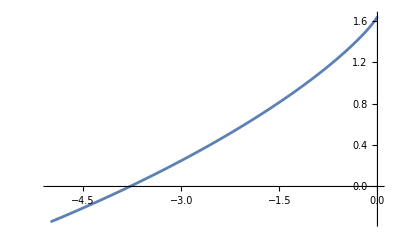

```mathematica
(*Mia's failed analytic attempt though it's close-ish if anyone needs this in the future.*)
g[R2_]:=NIntegrate[x^2/(√(x^2-Abs[R2]))*1/(ⅇ^(√(x^2-Abs[R2]))-1),{x,√Abs[R2]+0.0001,∞},WorkingPrecision->20]+NIntegrate[(-Sin[√Abs[x^2+R2]])/((Cos[√Abs[x^2+R2]]-1)^2+(Sin[√Abs[x^2+R2]])^2)*x^2/(√Abs[x^2+R2]),{x,0,-0.0001+√Abs[R2]}]

Plot[Re[g[R2]],{R2,-5,0}]
```